```mathematica
(*Compute the repo root from the notebook location*)repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

## Nodal Curve Parametrization

```mathematica
F1=MirrorCurveLocalF1[x,y,m,u]
```

-1/u+m/x+x+1/(x y)+y

```mathematica
m1=WeierstrassChangeOfVariables[{x,y}->{X,Y},m,u]
```

{x→(-9+36 u^2 (m+3 u)+6 X+√2 Y)/(6 u (-3+12 m u^2+2 X)),y→(36 u^2)/(3-12 m u^2-2 X)}

```mathematica
m2=WeierstrassChangeOfVariablesInverse[{X,Y}->{x,y},m,u]
```

{X→3/2-(6 u^2 (3+m y))/y,Y→-(54 √2 u^2 (-1+u (2 x+y)))/y}

```mathematica
Simplify[{x,y}/.m1/.m2]
```

{x,y}

```mathematica
Simplify[{X,Y}/.m2/.m1]
```

{X,Y}

```mathematica
Simplify[F1/.m1]
Numerator[%]
Simplify@Flatten[{Coefficient[%, {Y^2, X^4, X^3, X^2, X}], (%/.{X->0,Y->0}), -%/.Y->0}]//TableForm
```

(-27-5832 u^6+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-4 X^3-324 u^3 (-3+2 X)-108 m u^2 (-3+36 u^3+2 X)+Y^2)/(3 u (-3+12 m u^2+2 X) (-9+36 m u^2+108 u^3+6 X+√2 Y))

-27-5832 u^6+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-4 X^3-324 u^3 (-3+2 X)-108 m u^2 (-3+36 u^3+2 X)+Y^2

1
0
-4
0
27 (1-8 m u^2-24 u^3+16 m^2 u^4)
27 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6)
5832 u^6-1728 m^3 u^6-432 m^2 u^4 (-3+X)+(3-2 X)^2 (3+X)+324 u^3 (-3+2 X)+108 m u^2 (-3+36 u^3+2 X)

```mathematica
{MirrorCurveg2[m,u],MirrorCurveg3[m,u],MirrorCurvef3[X,m,u]}//TableForm
```

27 (1-8 m u^2-24 u^3+16 m^2 u^4)
27 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6)
5832 u^6-1728 m^3 u^6-432 m^2 u^4 (-3+X)+(3-2 X)^2 (3+X)+324 u^3 (-3+2 X)+108 m u^2 (-3+36 u^3+2 X)

```mathematica
Simplify[1/(544195584 u^8)Discriminant[MirrorCurvef3[X,m,u], X]]
MirrorCurveDelta[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
ClearAll[uvals];
uvals[m_]:=SortBy[Solve[delt[m,u]==0,u], Abs[u/.#]&];
```

```mathematica
(* for m=0, possible values of u *)
Solve[MirrorCurveDelta[0,u]==0,u]
```

{{u→0},{u→1/3},{u→-1/3 (-1)^(1/3)},{u→1/3 (-1)^(2/3)}}

```mathematica
(* for m=1, possible values of u *)
Solve[MirrorCurveDelta[1.,u]==0,u]
```

{{u→-3.02572},{u→-0.255099-0.221553 ⅈ},{u→-0.255099+0.221553 ⅈ},{u→0.263185}}

```mathematica
4(X-X0)^2(X+2X0)//Expand
Y^2-%/.{X->t^2-2X0, Y->2t(t^2-3X0)}//Simplify
```

4 X^3-12 X X0^2+8 X0^3

0

```mathematica
p1 = {X->t^2-2X0, Y->2t(t^2-3X0)};
p1 = p1/.{t->t/Sqrt[2]}//Simplify
Y^2-4(X-X0)^2(X+2X0)/.p1//Simplify
```

{X→1/2 (t^2-4 X0),Y→(t (t^2-6 X0))/(√2)}

0

```mathematica
First@Solve[Simplify[-12 X0^2/(8 X0^3)]==(-G2/-G3), X0]
```

{X0→-(3 G3)/(2 G2)}

```mathematica
-(3 MirrorCurveg3[m,u])/(2 MirrorCurveg2[m,u])//FullSimplify
```

(3+12 u^2 (-3 m-9 u+12 m^2 u^2+36 m u^3+2 (27-8 m^3) u^4))/(2+16 u^2 (-3 u+m (-1+2 m u^2)))

```mathematica
First@Solve[Simplify[-12 X0^2/(8 X0^3)]==(-MirrorCurveg2[m,u]/-MirrorCurveg3[m,u]), X0]
X0sol = FullSimplify[%, MirrorCurveDelta[m,u]==0]//Together
```

{X0→-(3 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

{X0→(3 (1-8 m u^2-32 u^3+16 m^2 u^4+108 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

```mathematica
X0tot1={X0->-3/4+t1^2/4+3 m u^2};
```

```mathematica
{x, y}/.m1/.p1
pxy = %/.X0tot1//Simplify
```

{(-9+36 u^2 (m+3 u)+t (t^2-6 X0)+3 (t^2-4 X0))/(6 u (-3+t^2+12 m u^2-4 X0)),(36 u^2)/(3-t^2-12 m u^2+4 X0)}

{(9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3)/(12 t^2 u-12 t1^2 u),-(36 u^2)/(t^2-t1^2)}

```mathematica
sol = FullSimplify[Solve[{(X0/.X0tot1)==(X0/.X0sol), delt[m,u]==0}, {m, u}]];
```

```mathematica
sol[[2]]
```

{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→(t1^(2/3) (3+t1)^(1/3))/(3 2^(1/3))}

```mathematica
9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3
FullSimplify[%/.sol[[2]]]
pxy1 = pxy/.{9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3->%}//Simplify
```

9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3

2 (t-t1)^2 (3+t+2 t1)

{((t-t1) (3+t+2 t1))/(6 (t+t1) u),-(36 u^2)/(t^2-t1^2)}

```mathematica
FullSimplify[X0sol/.sol[[2]]]
```

{X0→1/2 t1 (2+t1)}

```mathematica
-2+Sqrt[1+12m u^2]/.sol[[2]]//Simplify//PowerExpand
```

t1

```mathematica
t1s = 3(4m u^2+18u^3-1)/(1+12m u^2);
t1s/.sol[[2]]//Simplify
```

t1

```mathematica
X0s = (-3+12m u^2)/2-t1s//Simplify
```

(3 (1-16 m u^2-36 u^3+48 m^2 u^4))/(2+24 m u^2)

```mathematica
t/.Solve[X0==(X/.p1), t]
Solve[z==(t-%[[2]])/(t-%[[1]]), t]//Simplify
pxy2 = Together[pxy1/.First[%]]
```

{-√6 √X0,√6 √X0}

{{t→-(√6 √X0 (1+z))/(-1+z)}}

{-((-3-2 t1-√6 √X0+3 z+2 t1 z-√6 √X0 z) (-t1+√6 √X0+t1 z+√6 √X0 z))/(6 u (-1+z) (-t1-√6 √X0+t1 z-√6 √X0 z)),(36 u^2 (-1+z)^2)/(t1^2-6 X0-2 t1^2 z-12 X0 z+t1^2 z^2-6 X0 z^2)}

```mathematica
pxy2/.{X0->1/2t1^2+t1}
```

{-(((-3-2 t1-√6 √(t1+t1^2/2)+3 z+2 t1 z-√6 √(t1+t1^2/2) z) (-t1+√6 √(t1+t1^2/2)+t1 z+√6 √(t1+t1^2/2) z))/(6 u (-1+z) (-t1-√6 √(t1+t1^2/2)+t1 z-√6 √(t1+t1^2/2) z))),(36 u^2 (-1+z)^2)/(t1^2-6 (t1+t1^2/2)-2 t1^2 z-12 (t1+t1^2/2) z+t1^2 z^2-6 (t1+t1^2/2) z^2)}

```mathematica
Limit[pxy2, z->Infinity]/.sol[[2]]/.{X0->1/2t1^2+t1}//FullSimplify
```

{1/(2^(2/3) (t1/(3+t1))^(2/3)),-2^(1/3) (t1/(3+t1))^(1/3)}

```mathematica
Limit[pxy2, z->Infinity]//FullSimplify
%/.{X0->1/2t1^2+t1}//FullSimplify
%/.{t1->-2+Sqrt[1+12m u^2]}//Simplify
```

{-(3 t1+2 t1^2+3 √6 √X0+√6 t1 √X0-6 X0)/(6 t1 u-6 √6 u √X0),(36 u^2)/(t1^2-6 X0)}

{(3+t1)/(6 u),-(18 u^2)/(3 t1+t1^2)}

{(1+√(1+12 m u^2))/(6 u),(18 u^2)/(1-12 m u^2+√(1+12 m u^2))}

```mathematica
{dvec,avec} = RationalData[pxy2[[1]], z]
{evec, bvec} = RationalData[Factor[pxy2[[2]]/.{X0->x0sqrt^2},Extension->{Sqrt[6]}], z]/.{x0sqrt->Sqrt[X0]}
```

{{1,1,-1,-1},{(3+2 t1+√6 √X0)/(3+2 t1-√6 √X0),(t1-√6 √X0)/(t1+√6 √X0),1,(t1+√6 √X0)/(t1-√6 √X0)}}

{{2,-1,-1},{1,(t1+√6 √X0)/(t1-√6 √X0),(t1-√6 √X0)/(t1+√6 √X0)}}

```mathematica
(3+2 t1+√6 √X0)/(3+2 t1-√6 √X0)((t1-√6 √X0)/(t1+√6 √X0))^2
%/.{X0->1/2t1^2+t1}//Simplify
```

((t1-√6 √X0)^2 (3+2 t1+√6 √X0))/((3+2 t1-√6 √X0) (t1+√6 √X0)^2)

1

#### Can we write α β in terms of b

```mathematica
bTot1={b->(t1-√6 √X0)/(t1+√6 √X0)};
```

```mathematica
(t1-√6 √X0)/(t1+√6 √X0)/.{X0->t1^2/2+t1}//FullSimplify
%/.{√(t1 (2+t1))->sq}
t1 (2+t1)-sq^2/.First@Solve[b==%, sq]//Expand//FullSimplify
Solve[%==0, t1]
```

(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)

(-3+√3 sq-2 t1)/(3+t1)

-1/3 (3+t1) (3 (1+b)^2+t1+b (4+b) t1)

{{t1→-3},{t1→-(3 (1+2 b+b^2))/(1+4 b+b^2)}}

```mathematica
{(3+t1)/(6 u),-(18 u^2)/(3 t1+t1^2)}/.sol2[[1]]//Simplify
Assuming[b>1, Simplify[%/.{t1->-(3 (1+2 b+b^2))/(1+4 b+b^2)}]]
```

{(-1/2)^(2/3)/(t1/(3+t1))^(2/3),-(-1)^(2/3) 2^(1/3) (t1/(3+t1))^(1/3)}

{1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)}

```mathematica
(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)/.{t1->-2+Sqrt[1+12m u^2]}
FullSimplify[%, MirrorCurveDelta[m,u]==0]
```

(-3-2 (-2+√(1+12 m u^2))+√3 √(√(1+12 m u^2) (-2+√(1+12 m u^2))))/(1+√(1+12 m u^2))

(1-2 √(1+12 m u^2)+√(3+36 m u^2-6 √(1+12 m u^2)))/(1+√(1+12 m u^2))

## Kerr Doran: Imaginary part of period

```mathematica
{dvec,avec}={{1,1,-1,-1},{1/b^2,b,1,1/b}};
{evec,bvec}={{2,-1,-1},{1,1/b,b}};
```

```mathematica
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
```

-(BW[1/b^3]-3 BW[1/b^2]+2 BW[1/b]-3 BW[b]+BW[b^2])/(2 π)

```mathematica
BWRules = {{BW[z_]:>BW[1-1/z]}, {BW[z_]:>BW[1/(1-z)]}, {BW[z_]:>-BW[1/z]}, {BW[z_]:>-BW[1-z]}, {BW[z_]:>-BW[-z/(1-z)]}};
BWFiveTerm[x_,y_] := BW[x] + BW[y] + BW[(1-x)/(1-x y)] + BW[1-x y] + BW[(1-y)/(1-x y)];
BWEval={BW[x_]:>Im[PolyLog[2, x]]+Arg[1-x]Log[Abs[x]]};
```

```mathematica
Cases[A, BW[__], Infinity]
```

{BW[1/b^3],BW[1/b^2],BW[1/b],BW[b],BW[b^2]}

```mathematica
BW[1/b^n]/.BWRules
```

{BW[1-b^n],BW[1/(1-b^-n)],-BW[b^n],-BW[1-b^-n],-BW[-b^-n/(1-b^-n)]}

```mathematica
A1 = A/.{BW[1/b]->-BW[b],BW[1/b^2]->-BW[b^2], BW[1/b^3]->-BW[b^3]}//Simplify
```

(5 BW[b]-4 BW[b^2]+BW[b^3])/(2 π)

## Kerr Doran: Full period

```mathematica
{dvec,avec}={{1,1,-1,-1},{1/b^2,b,1,1/b}};
{evec,bvec}={{2,-1,-1},{1,1/b,b}};
{Xat0,wat0} = {1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)};
XatInf=Xat0;
```

```mathematica
b0 = 1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

b1 = -1/2/Pi Log[wat0](Log[Xat0]-Log[XatInf])//Simplify;

b2 = 1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

b3 = -1/2/Pi Log[XatInf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = b0 + b1 + b2 + b3//Simplify
```

1/(6 π)(3 (Log[1/b]+Log[b]) Log[1/(2+1/b+b)^(2/3)]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[2+1/b+b]-3 (Li2[1/b^3]-Li2[1/b^2]-Li2[b]+Li2[b^2]-2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])+Log[1-b] Log[1/b]+(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]+2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])+Log[1-1/b^3] (Log[1/b^2]-Log[b])-Log[1-1/b^2] (Log[1/b]-Log[b])+Log[(-1+b)/b] Log[b]-2 (Li2[b]+Log[1-b] Log[b])-(Log[1/b]-Log[b]) Log[1-b^2]))

```mathematica
Li2Rules = {{Li2[z_]:>-Li2[1/z]-Pi^2/6-1/2 Log[-1/z]^2}, {Li2[z_]:>-Li2[1-z]+Pi^2/6-Log[z]Log[1-z]}};
```

```mathematica
Li2FiveTerm[x_, y_] = Simplify[L[x]+L[y]+L[1-x y]+L[(1-x)/(1-x y)]+L[(1-y)/(1-x y)]-3Pi^2/6/.{L[z_]:>Li2[z]+1/2Log[z]Log[1-z]}];
```

```mathematica
Li2Eval = {Li2[z_]:>PolyLog[2, z]};
```

```mathematica
Cases[B,Li2[_],Infinity]//DeleteDuplicates
```

{Li2[1/b^3],Li2[1/b^2],Li2[b],Li2[b^2],Li2[1/b]}

```mathematica
Li2[1/b^3]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2),1/6 (π^2-6 Li2[1-1/b^3]-6 Log[1-1/b^3] Log[1/b^3])}

```mathematica
Li2[1/b^2]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b^2]-3 Log[-b^2]^2),1/6 (π^2-6 Li2[1-1/b^2]-6 Log[1-1/b^2] Log[1/b^2])}

```mathematica
Li2[1/b]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b]-3 Log[-b]^2),1/6 (π^2-6 Li2[(-1+b)/b]-6 Log[1/b] Log[(-1+b)/b])}

```mathematica
rules={
Li2[1/b^3]->1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2),
Li2[1/b^2]->1/6 (-π^2-6 Li2[b^2]-3 Log[-b^2]^2),
Li2[1/b]->1/6 (-π^2-6 Li2[b]-3 Log[-b]^2)
};
temp = B/.rules/.{Li2[_]:>0}//Simplify
```

1/(12 π)(-6 Log[1-b] Log[1/b]-6 Log[1/b^2] Log[(-1+b)/b]-6 Log[1/b] Log[(-1+b)/b]+6 Log[-b]^2-6 Log[1-1/b^3] (Log[1/b^2]-Log[b])+6 Log[1-1/b^2] (2 Log[1/b^2]+Log[1/b]-Log[b])+12 Log[1-b] Log[b]-6 Log[(-1+b)/b] Log[b]-9 Log[-b^2]^2+3 Log[-b^3]^2+6 Log[1/b] Log[1/(2+1/b+b)^(2/3)]+6 Log[b] Log[1/(2+1/b+b)^(2/3)]+2 Log[1/b^2] Log[2+1/b+b]-2 Log[1/b] Log[2+1/b+b]+2 Log[b] Log[2+1/b+b]+6 Log[1/b] Log[1-b^2]-6 Log[b] Log[1-b^2])

```mathematica
-1+b^3//Factor
```

(-1+b) (1+b+b^2)

```mathematica
12Pi temp/2/3//Expand
%/.{Log[x_/y_]:>Log[x]-Log[y]}/.{Log[x_*y_]:>Log[x]+Log[y]}/.{Log[b^n_]:>n Log[b]}
Map[Together, %, Infinity]/.{Log[x_/y_]:>Log[x]-Log[y]}/.{Log[x_*y_]:>Log[x]+Log[y]}/.{Log[b^n_]:>n Log[b]}
%/.{Log[1-b^2]->Log[1-b]+Log[1+b], Log[-1+b^2]->Log[b-1]+Log[1+b],Log[-1+b^3]->Log[b-1]+Log[1+b+b^2]}//ExpandAll//Simplify
temp2 = %/.{-2 ⅈ π+2 Log[1-b]-2 Log[-1+b]->-4 ⅈ π}
```

-Log[1-1/b^3] Log[1/b^2]+2 Log[1-1/b^2] Log[1/b^2]+Log[1-1/b^2] Log[1/b]-Log[1-b] Log[1/b]-Log[1/b^2] Log[(-1+b)/b]-Log[1/b] Log[(-1+b)/b]+Log[-b]^2+Log[1-1/b^3] Log[b]-Log[1-1/b^2] Log[b]+2 Log[1-b] Log[b]-Log[(-1+b)/b] Log[b]-3/2 Log[-b^2]^2+1/2 Log[-b^3]^2+Log[1/b] Log[1/(2+1/b+b)^(2/3)]+Log[b] Log[1/(2+1/b+b)^(2/3)]+1/3 Log[1/b^2] Log[2+1/b+b]-1/3 Log[1/b] Log[2+1/b+b]+1/3 Log[b] Log[2+1/b+b]+Log[1/b] Log[1-b^2]-Log[b] Log[1-b^2]

3 Log[1-1/b^3] Log[b]-6 Log[1-1/b^2] Log[b]+3 Log[1-b] Log[b]+2 (Log[-1+b]-Log[b]) Log[b]+(ⅈ π+Log[b])^2-3/2 (ⅈ π+2 Log[b])^2+1/2 (ⅈ π+3 Log[b])^2-2 Log[b] Log[1-b^2]

-(π-ⅈ Log[b])^2+3/2 (π-2 ⅈ Log[b])^2-1/2 (π-3 ⅈ Log[b])^2+3 Log[1-b] Log[b]+2 (Log[-1+b]-Log[b]) Log[b]-2 Log[b] Log[1-b^2]-6 Log[b] (-2 Log[b]+Log[-1+b^2])+3 Log[b] (-3 Log[b]+Log[-1+b^3])

1/2 Log[b] (-2 ⅈ π+2 Log[1-b]-2 Log[-1+b]+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

1/2 Log[b] (-4 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

```mathematica
FullSimplify[-2 ⅈ π+2 Log[1-b]-2 Log[-1+b], Im[b]>0]
```

-4 ⅈ π

```mathematica
Together[(B/.rules)-temp]+temp2/2/Pi
%/.{b->-0.7251497610490148665275651524636838940601276942612714222276`38.51933138562852+0.6885911878978387285805195905580644422553067984717644767418`38.67353511270891 ⅈ}/.Li2Eval
```

(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (-4 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4 π)

6.047239614429887673081434793311933591+1.157322100746665312432350757333190625 ⅈ

```mathematica
(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (+5I Pi+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4π)
%/.{b->-0.7251497610490148665275651524636838940601276942612714222276`38.51933138562852+0.6885911878978387285805195905580644422553067984717644767418`38.67353511270891 ⅈ}/.Li2Eval
```

(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (5 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4 π)

0.687631197635847659612645389468778082+1.157322100746665312432350757333190625 ⅈ

## From first principles

```mathematica
fanGen={{0,0},{1,0},{-1,-1},{-1,0},{0,1}};
```

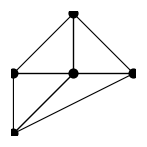

```mathematica
Graphics[{EdgeForm[Black],FaceForm[],Polygon@Take[fanGen,-4], Line/@Thread[{Take[fanGen,-4], First[fanGen]}, List, 1], PointSize[.05],Point@fanGen}]
```

```mathematica
fanV = ArrayPad[fanGen, {{0,0}, {0,1}}, 1]
```

{{0,0,1},{1,0,1},{-1,-1,1},{-1,0,1},{0,1,1}}

```mathematica
Solve[Thread[fanVᵀ.Array[a,5]==0], Array[a,5], Integers]
fanQ = Array[a,5]/.First[%]/.{{C[1]->-2,C[2]->1},{C[1]->-1,C[2]->0}}
fanVQ = Join[fanVᵀ, %]ᵀ;
fanVQ//MatrixForm
```

{{a[1]→ConditionalExpression[C[1], (C[1]|C[2])∈ℤ],a[2]→ConditionalExpression[C[2], (C[1]|C[2])∈ℤ],a[3]→ConditionalExpression[-C[1]-2 C[2], (C[1]|C[2])∈ℤ],a[4]→ConditionalExpression[C[1]+3 C[2], (C[1]|C[2])∈ℤ],a[5]→ConditionalExpression[-C[1]-2 C[2], (C[1]|C[2])∈ℤ]}}

{{-2,1,0,1,0},{-1,0,1,-1,1}}

(0 | 0 | 1 | -2 | -1
1 | 0 | 1 | 1 | 0
-1 | -1 | 1 | 0 | 1
-1 | 0 | 1 | 1 | -1
0 | 1 | 1 | 0 | 1)

```mathematica
CSMDef = Thread[Array[z,Length[fanQ]]->Table[Product[a[i]^fanQ[[A, i]], {i,1,5}], {A, 1, Length[fanQ]}]]
```

{z[1]→(a[2] a[4])/a[1]^2,z[2]→(a[3] a[5])/(a[1] a[4])}

```mathematica
H[X_,Y_]=Sum[a[i]X^fanVQ[[i,1]]Y^fanVQ[[i,2]], {i,Length[fanVQ]}]
```

a[1]+X a[2]+a[3]/(X Y)+a[4]/X+Y a[5]

```mathematica
H[X,Y]/a[1]/.{X->xc X, Y->yc Y}//Expand
H1[X_,Y_]=%/.{xc->a[1]/a[2], yc->a[1]/a[5]}/.{(a[2] a[4])/a[1]^2->z[1],(a[3] a[5])/(a[1] a[4])->z[2]}/.{(a[2] a[3] a[5])/a[1]^3->z[1]z[2]}
```

1+(X xc a[2])/a[1]+a[3]/(X xc Y yc a[1])+a[4]/(X xc a[1])+(Y yc a[5])/a[1]

1+X+Y+z[1]/X+(z[1] z[2])/(X Y)

## Periods from gamma soln

```mathematica
Gamma/@(fanQᵀ.{n1+r1,n2+r2}+1)
expr1 = z1^(n1+r1) z2^(n2+r2)/Times@@%
expr2 = %/.{Gamma[1-n2-2 (n1+r1)-r2]->Pi (n2+2 (n1+r1)+r2)/Sin[Pi (n2+2 (n1+r1)+r2)]/Gamma[1+n2+2 (n1+r1)+r2]}
```

{Gamma[1-n2-2 (n1+r1)-r2],Gamma[1+n1+r1],Gamma[1+n2+r2],Gamma[1+n1-n2+r1-r2],Gamma[1+n2+r2]}

(z1^(n1+r1) z2^(n2+r2))/(Gamma[1+n1+r1] Gamma[1+n1-n2+r1-r2] Gamma[1-n2-2 (n1+r1)-r2] Gamma[1+n2+r2]^2)

(z1^(n1+r1) z2^(n2+r2) Gamma[1+n2+2 (n1+r1)+r2] Sin[π (n2+2 (n1+r1)+r2)])/(π (n2+2 (n1+r1)+r2) Gamma[1+n1+r1] Gamma[1+n1-n2+r1-r2] Gamma[1+n2+r2]^2)

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Limit[%, {n1,n2}->{0,0}]
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z1]

```mathematica
Simplify[D[expr2, r1]/.{r1->0,r2->0}]
Limit[%, {n1->0,n2->0}]
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (4 n1 π Cos[(2 n1+n2) π]+2 n2 π Cos[(2 n1+n2) π]-2 Sin[(2 n1+n2) π]+2 n1 Log[z1] Sin[(2 n1+n2) π]+n2 Log[z1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+4 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+2 n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z1]

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

0

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

ConditionalExpression[(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2), 2 n1+n2<1]

```mathematica
Simplify[D[expr2, r1]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (4 n1 π Cos[(2 n1+n2) π]+2 n2 π Cos[(2 n1+n2) π]-2 Sin[(2 n1+n2) π]+2 n1 Log[z1] Sin[(2 n1+n2) π]+n2 Log[z1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+4 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+2 n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

(2 z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
vpi1[z1_,z2_,0,0]:=Log[z1];
vpi1[z1_,z2_,n1_Integer,n2_Integer]:=0/;n1<n2;
vpi1[z1_,z2_,n1_Integer,n2_Integer]:=(2 z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)/;n1>=n2;
```

#### t2?

```mathematica
Simplify[D[expr1, r2]/.{r1->0,r2->0}]
Limit[%, {n1,n2}->{0,0}]
```

(z1^n1 z2^n2 (Log[z2]+PolyGamma[0,1-2 n1-n2]+PolyGamma[0,1+n1-n2]-2 PolyGamma[0,1+n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z2]

```mathematica
Simplify[D[expr2, r2]/.{r1->0,r2->0}]
Limit[%, {n1->0,n2->0}]
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (2 n1 π Cos[(2 n1+n2) π]+n2 π Cos[(2 n1+n2) π]-Sin[(2 n1+n2) π]+2 n1 Log[z2] Sin[(2 n1+n2) π]+n2 Log[z2] Sin[(2 n1+n2) π]+(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]-2 (2 n1+n2) PolyGamma[0,1+n2] Sin[(2 n1+n2) π]+2 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z2]

```mathematica
Simplify[D[expr1, r2]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z2]+PolyGamma[0,1-2 n1-n2]+PolyGamma[0,1+n1-n2]-2 PolyGamma[0,1+n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

0

```mathematica
Simplify[D[expr2, r2]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (2 n1 π Cos[(2 n1+n2) π]+n2 π Cos[(2 n1+n2) π]-Sin[(2 n1+n2) π]+2 n1 Log[z2] Sin[(2 n1+n2) π]+n2 Log[z2] Sin[(2 n1+n2) π]+(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]-2 (2 n1+n2) PolyGamma[0,1+n2] Sin[(2 n1+n2) π]+2 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

(z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
vpi2[z1_,z2_,0,0]:=Log[z2];
vpi2[z1_,z2_,n1_Integer,n2_Integer]:=0/;n1<n2;
vpi2[z1_,z2_,n1_Integer,n2_Integer]:=(z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)/;n1>=n2;
```

#### continue

```mathematica
Table[vpi1[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

2 z1+3 z1^2+(20 z1^3)/3-4 z1 z2-24 z1^2 z2-120 z1^3 z2+30 z1^2 z2^2+420 z1^3 z2^2-(1120 z1^3 z2^3)/3+Log[z1]

```mathematica
Table[vpi2[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

z1+(3 z1^2)/2+(10 z1^3)/3-2 z1 z2-12 z1^2 z2-60 z1^3 z2+15 z1^2 z2^2+210 z1^3 z2^2-(560 z1^3 z2^3)/3+Log[z2]

```mathematica
Table[vpi1[z1,z2,n1,n2]-2vpi2[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

Log[z1]-2 Log[z2]

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
FullSimplify[Limit[%, {n1,n2}->{0,0}]]
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

-π^2+Log[z1]^2

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

$Aborted

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,2nn1+nn2>=1,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

-((4 z1^n1 (-z2)^n2 (-1+2 n1+n2)! (2 EulerGamma-2 HarmonicNumber[-1+2 n1+n2]-Log[z1]+PolyGamma[0,1+n1]+PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2))

```mathematica
Simplify[D[expr2, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,2nn1+nn2<1,(nn1|nn2)∈NonNegativeIntegers}, FullSimplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] ((8-4 (2 n1+n2) Log[z1]+(2 n1+n2)^2 Log[z1]^2+2 (2 n1+n2) (2-(2 n1+n2) Log[z1]) PolyGamma[0,1+n1]+(2 n1+n2)^2 (PolyGamma[0,1+n1]^2-PolyGamma[1,1+n1])) Sin[(2 n1+n2) π]+2 (2 n1+n2) (-2+(2 n1+n2) Log[z1]-(2 n1+n2) PolyGamma[0,1+n1]) (2 π Cos[(2 n1+n2) π]-PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π])-(2 n1+n2)^2 (-8 π Cos[(2 n1+n2) π] PolyGamma[0,1+2 n1+n2]-PolyGamma[0,1+n1-n2]^2 Sin[(2 n1+n2) π]-4 PolyGamma[0,1+2 n1+n2]^2 Sin[(2 n1+n2) π]+(4 π^2+PolyGamma[1,1+n1-n2]-4 PolyGamma[1,1+2 n1+n2]) Sin[(2 n1+n2) π]+4 PolyGamma[0,1+n1-n2] (π Cos[(2 n1+n2) π]+PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))))/((2 n1+n2)^3 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
expr3 = FullSimplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
```

(z1^n1 z2^n2 ((HarmonicNumber[n1]-2 HarmonicNumber[-2 n1-n2]+HarmonicNumber[n1-n2]-Log[z1])^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
expr4 = D[expr2, {r1,2}]/.{r1->0,r2->0};
```

```mathematica
Limit[expr4,{n1->0,n2->0}]//FullSimplify
```

-π^2+Log[z1]^2

```mathematica
Table[Simplify[Limit[expr3,{n1->N1,n2->N2}]], {N1,0,3},{N2,0,3}]//MatrixForm
```

(-π^2+Log[z1]^2 | -4 z2 | -z2^2 | -(4 z2^3)/9
4 z1 Log[z1] | -8 z1 z2 (2+Log[z1]) | 6 z1 z2^2 | (8 z1 z2^3)/3
2 z1^2 (2+3 Log[z1]) | -16 z1^2 z2 (5+3 Log[z1]) | 4 z1^2 z2^2 (46+15 Log[z1]) | -40 z1^2 z2^3
4/3 z1^3 (9+10 Log[z1]) | -8 z1^3 z2 (47+30 Log[z1]) | 8 z1^3 z2^2 (247+105 Log[z1]) | -16/9 z1^3 z2^3 (1513+420 Log[z1]))

### Picard Fuchs

```mathematica
PF1[f_,z1_,z2_]:=z1 D[z1 D[f, z1]-z2 D[f, z2], z1]-z1 (2z1 D[f + 2 z1 D[f, z1] + z2 D[f, z2], z1]+z2 D[f + 2 z1 D[f, z1] +  z2 D[f, z2], z2]);
```

```mathematica
PF2[f_,z1_,z2_]:=z2 D[z2 D[f, z2], z2]-z2 (z2 D[2 z1 D[f, z1] + z2 D[f, z2], z2]-z1 D[2 z1 D[f, z1] + z2 D[f, z2], z1]);
```

```mathematica
PF1[z1^2+z2^2,z1,z2]
```

4 z1^2-z1 (20 z1^2+10 z2^2)

```mathematica
Series[Sum[vpi1[z1,z2,n1,n2], {n1,0,10},{n2,0,10}], {z1,0,10},{z2,0,10}];
Simplify[z2 D[%, z2]];
PF1[%,z1,z2]//Simplify
```

O[z1]^11

```mathematica
PF2[z1 D[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z1],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
```

1/27 (4 lam f^(0,1)[ut,lam]+12 lam^2 f^(0,2)[ut,lam]+4 lam^3 f^(0,3)[ut,lam]-ut f^(1,0)[ut,lam]-3 lam ut f^(1,1)[ut,lam]-9 lam f^(1,2)[ut,lam]-3 ut^2 f^(2,0)[ut,lam]+9 ut f^(2,1)[ut,lam]-3 lam ut^2 f^(2,1)[ut,lam]-ut^3 f^(3,0)[ut,lam])

```mathematica
PF1[z2 D[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z2],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
```

1/9 lam (-2 f^(0,1)[ut,lam]-6 lam f^(0,2)[ut,lam]-2 lam^2 f^(0,3)[ut,lam]+2 ut f^(1,1)[ut,lam]+lam ut f^(1,2)[ut,lam]+6 f^(2,0)[ut,lam]+6 lam f^(2,1)[ut,lam]+ut^2 f^(2,1)[ut,lam]+3 ut f^(3,0)[ut,lam])

```mathematica
9 PF2[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
%//Expand
```

ut f^(1,0)[ut,lam]-9 f^(1,1)[ut,lam]+4 lam (f^(0,1)[ut,lam]+lam f^(0,2)[ut,lam]+ut f^(1,1)[ut,lam])+ut^2 f^(2,0)[ut,lam]

4 lam f^(0,1)[ut,lam]+4 lam^2 f^(0,2)[ut,lam]+ut f^(1,0)[ut,lam]-9 f^(1,1)[ut,lam]+4 lam ut f^(1,1)[ut,lam]+ut^2 f^(2,0)[ut,lam]

## Numerical checks

```mathematica
(* varpi2 with Richardson *)
varpi2[u_,lam_]:=With[{Nn=1024, d=15}, Module[{terms,sums}, 
terms=Table[Sum[If[Mod[n-2l, 3]==0, (n-1)!/Factorial[(n-2l)/3]^2/Factorial[l]/Factorial[(n+l)/3] lam^l, 0], {l,0,n}]u^n, {n, 2, Nn}];
sums=-Log[u]-Accumulate[terms];
Table[Sum[sums[[n+k]](n+k)^d(-1)^(k+d)/k!/(d-k)!, {k, 0, d}], {n, 1, Length[sums]-d}]
]];
```

```mathematica
(* varpi3 with Richardson *)
varpi3[z_,lam_]:=With[{Nn=200, d=5}, Module[{terms,sums}, 
terms=Table[Sum[(2n)!/n/Factorial[n-l]^2/Factorial[l]^2(HarmonicNumber[n-l]+HarmonicNumber[l]-2HarmonicNumber[2n]+1/n) lam^l, {l,0,n}]z^n, {n, 1, Nn}];
sums=-Log[z]^2+(2Log[z]+Log[lam])Last[varpi2[z,lam]]-2Accumulate[terms];
Table[Sum[sums[[n+k]](n+k)^d(-1)^(k+d)/k!/(d-k)!, {k, 0, d}], {n, 1, Length[sums]-d}]
]];
```

```mathematica
u0 = First@SortBy[u/.Solve[m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0/.{m->2}, u, WorkingPrecision->300], Abs]
```

0.227203634857985759161254765346706290384224015255178461093477420691304642267091217742189796411130923115944638285781096295310110730752078711791964944775615339522431160058805630903139642604728284338325494815447595924727522181455304313717828188321139203654575906882416423394662141575571995897076683668046

```mathematica
target=1.1573221007466653124323507573331906
```

1.157322100746665312432350757333191

```mathematica
1.271036692098228453117342
```

```mathematica
Last@varpi2[u0, N[2,300]]
```

1.271036692098228453117342128887728881141326216177305025262608167072939021033408471101716154596023394884084687961317683553858664268272421469174377605909422062516151427111375217763095564157298455233666971842732642885922422955025994501096701002268498533211126023272

```mathematica
m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{u->-1/u, m->lam}//Simplify//Together
```

(-27+16 lam^3+36 lam u-8 lam^2 u^2-u^3+lam u^4)/u^4

```mathematica
1728g2^3/(g2^3-27g3^2)//FullSimplify
eqn = %-j//Simplify//Together//Numerator//Simplify
```

((1+8 u^2 (-3 u+m (-1+2 m u^2)))^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4))

1-72 u^3+1728 u^6-(13824+j) u^9-6144 m^5 u^10+27 j u^12+4096 m^6 u^12-768 m^4 u^8 (-5+24 u^3)-16 m^3 u^6 (80-1152 u^3+j u^6)+8 m^2 u^4 (30-864 u^3+(3456+j) u^6)+m u^2 (-24+1152 u^3-(13824+j) u^6+36 j u^9)

```mathematica
Discriminant[eqn, u]//FullSimplify
```

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-1024 m^3 (4782969+128 m^3 (98415+128 m^3 (756-j+256 m^3))))

```mathematica
Expand[(-387420489-1024 m^3 (4782969+128 m^3 (98415+128 m^3 (756-j+256 m^3))))]+((27+256m^3)(243+256m^3)^3-2^24j m^9)//Simplify
```

0

```mathematica
A1/.{b->}/.BWEval
```

1/(2 π)(Im[PolyLog[2,b^3]]+5 (Im[PolyLog[2,b]]+Arg[1-b] Log[Abs[b]])-4 (Im[PolyLog[2,b^2]]+Arg[1-b^2] Log[Abs[b]^2])+Arg[1-b^3] Log[Abs[b]^3])

```mathematica
uvals[N[1,30]]
```

{{u→0.26318526921874357906535706028},{u→-0.2550986687263150511885485324-0.2215528143588283005513899855 ⅈ},{u→-0.2550986687263150511885485324+0.2215528143588283005513899855 ⅈ},{u→-3.025715204493386203960987268}}

```mathematica
With[{m=N[1,30]},{m,u/.uvals[m][[1]]}]
{Solve[(m/.sol[[4]])==%[[1]], t1],Solve[(u/.sol[[4]])==%[[2]], t1]}
```

{1.,0.26318526921874357906535706028}

$Aborted

```mathematica
sol[[4]]
```

{m→(3 (-1/2)^(1/3) (-1+t1) (-((-3+t1) t1^2))^(1/3))/(2 t1^2),u→-1/3 (-1/2)^(1/3) (-((-3+t1) t1^2))^(1/3)}

```mathematica
sol[[2]]
```

{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→(t1^(2/3) (3+t1)^(1/3))/(3 2^(1/3))}

```mathematica
b/.bTot1/.{}
```

(t1-√6 √X0)/(t1+√6 √X0)

```mathematica
delt[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
X0sol
```

{X0→(3 (1-8 m u^2-32 u^3+16 m^2 u^4+108 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

```mathematica
Solve[-3+t^2+12 m u^2-4 X0==0, t]
```

{{t→-√(3-12 m u^2+4 X0)},{t→√(3-12 m u^2+4 X0)}}

```mathematica
FullSimplify@Together[3-12 m u^2+4 X0/.X0sol]
FullSimplify[%, delt[m,u]==0]
```

(3 (3-28 m u^2-88 u^3+80 m^2 u^4+96 m u^5+8 (27-8 m^3) u^6))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))

(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))

```mathematica
delt[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
t1sq=(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)));
```

```mathematica
sol2 = Assuming[t1>0, Simplify@Solve[{(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))==t1^2, m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0}, {m,u}]]
```

{{m→-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3)),u→-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3)},{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→((t1^2 (3+t1))^(1/3))/(3 2^(1/3))},{m→(3 (-1)^(2/3) (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→((-t1)^(2/3) (3+t1)^(1/3))/(3 2^(1/3))},{m→(3 (-1/2)^(1/3) (3-t1)^(1/3) (-1+t1))/(2 t1^(4/3)),u→-1/3 (-1/2)^(1/3) (-((-3+t1) t1^2))^(1/3)},{m→-(3 (3-t1)^(1/3) (-1+t1))/(2 2^(1/3) t1^(4/3)),u→((-((-3+t1) t1^2))^(1/3))/(3 2^(1/3))},{m→-(3 (-1)^(2/3) (3-t1)^(1/3) (-1+t1))/(2 2^(1/3) t1^(4/3)),u→((-1)^(2/3) (-((-3+t1) t1^2))^(1/3))/(3 2^(1/3))}}

```mathematica
NSolve[(m/.sol2[[1]])==1,t1]
```

{{t1→-0.775755-0.553985 ⅈ},{t1→-0.775755+0.553985 ⅈ},{t1→-0.646782}}

```mathematica
NSolve[(m/.sol2[[2]])==1,t1]
```

{{t1→-12.529}}

```mathematica
NSolve[(m/.sol2[[3]])==1,t1]
```

{{t1→-0.775755+0.553985 ⅈ}}

```mathematica
NSolve[(m/.#)==1,t1]&/@sol2
Flatten[t1/.%]//DeleteDuplicates
```

{{{t1→-0.775755-0.553985 ⅈ},{t1→-0.775755+0.553985 ⅈ},{t1→-0.646782}},{{t1→-12.529}},{{t1→-0.775755+0.553985 ⅈ}},{{t1→0.775755-0.553985 ⅈ}},{{t1→0.646782}},{{t1→12.529},{t1→0.775755+0.553985 ⅈ}}}

{-0.775755-0.553985 ⅈ,-0.775755+0.553985 ⅈ,-0.646782,-12.529,-0.775755+0.553985 ⅈ,0.775755-0.553985 ⅈ,0.646782,12.529,0.775755+0.553985 ⅈ}

```mathematica
With[{m=N[1,20]},-2+Sqrt[1+12m Echo[First[(u/.uvals[m])]]^2]]
```

0.2631852692187435791

-0.6467824154242931072

```mathematica
First[sol2]/.{t1->-0.64678241542429310724842125241159423282`19.373077221607886}
```

{m→1.+0. ⅈ,u→0.2631852692187435791+0. ⅈ}

```mathematica
FullSimplify[delt[m,u]/.sol2[[1]],-3<t1<0]
```

0

```mathematica
FullSimplify[t1sq/.sol2[[1]],-3<t1<0]
```

t1^2

```mathematica
FullSimplify[X0/.X0sol/.sol2[[1]],-3<t1<0]//Expand
```

t1+t1^2/2

```mathematica
FullSimplify[b/.bTot1/.{X0->t1+t1^2/2}, -3<t1<0]
Solve[%==b,t1]
m/.sol2[[1]]/.First[%]//FullSimplify
```

(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{t1→-(3 (1+2 b+b^2))/(1+4 b+b^2)}}

-((1+b+b^2) (-b/(1+b (4+b)))^(1/3))/((1+b)^2 (-1+(2 b)/(1+b (4+b)))^(1/3))

```mathematica
FunctionRange[{(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1), -3<t1<0},t1,b, Reals]
```

b≥1

```mathematica
FunctionRange[{1/2t1^2+t1, -3<t1<0},t1,X0]
```

-1/2≤X0<3/2

```mathematica
Limit[pxy2, z->0]/.{X0->1/2t1^2+t1}/.sol2[[1]]
FullSimplify[%, -3<t1<0]
```

{((-1/2)^(2/3) (-3-2 t1-√6 √(t1+t1^2/2)) (-t1+√6 √(t1+t1^2/2)))/(t1^(2/3) (3+t1)^(1/3) (-t1-√6 √(t1+t1^2/2))),(2 (-1)^(2/3) 2^(1/3) t1^(4/3) (3+t1)^(2/3))/(t1^2-6 (t1+t1^2/2))}

{(-1/2)^(2/3)/(t1/(3+t1))^(2/3),2^(1/3) (-t1/(3+t1))^(1/3)}

```mathematica
m/.sol2[[1]]
```

-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3))

```mathematica
FunctionRange[{-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3), -3<t1<0}, t1, x]
```

False

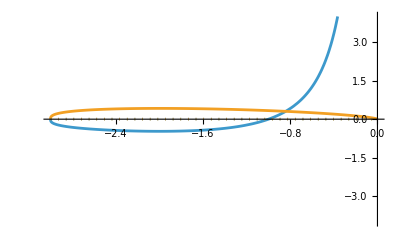

```mathematica
ReImPlot[{-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3)),-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3)}, {t1,-3,0},
PlotRange->{Automatic, {-4, 4}}
]
```

```mathematica
-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3))/.{t1->-2}//N
```

-0.47247

```mathematica
tudata = Table[{-2+Sqrt[1+12 m (u/.First[uvals[m]])^2], u/.First[uvals[m]]}, {m, -3/(4 2^(2/3)), 10, .01}];
```

```mathematica
tudatareal = Select[tudata, FreeQ[#,Complex]&];
```

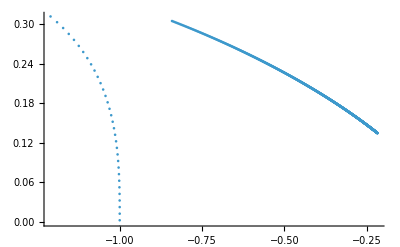

```mathematica
ListPlot[tudatareal]
```

```mathematica
bTot1
```

{b→(t1-√6 √X0)/(t1+√6 √X0)}

```mathematica
First[u/.uvals[1.]]//N
{Sqrt[t1sq],-2+Sqrt[1+12m u^2], 3(4m u^2+18u^3-1)/(12m u^2+1)}/.{m->1,u->%}
t1^2/2+t1/.{t1->Last[%]}
```

0.263185

{0.646782,-0.646782,-0.646782}

-0.437619

```mathematica
First[u/.uvals[1.]]//N
X0/.X0tot1/.{m->1,u->%}/.{t1->-0.6467824154242932}
```

0.263185

-0.437619

```mathematica
With[{m=N[2,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]];
A1/.{b->%}/.BWEval
```

u = 0.227203634857985759161254765346706290384

b = -0.79822170716314772598004515101171238668+0.60236376568776946837965610457745714968 ⅈ

1.13841093952205567492550624228156048

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]]
B/.{b->%}/.Li2Eval
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

-0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

0.523598775598298873077107230546583814+1.15732210074666531243235075733319062 ⅈ

```mathematica
N[Pi/6,40]
```

0.5235987755982988730771072305465838140329

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
Chop@Limit[pxy2/.u->u0, z->0]
]]
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

{1.4902161200999536481163868423786267429,0.81917251339616443969957118834242704035}

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]];
{{1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)}}/.{b->%}
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

{{1.490216120099953648116386842378626743+0. ⅈ,0.81917251339616443969957118834242704035+0. ⅈ}}

## Further Numerical checks

```mathematica
mvals=RandomComplex[{-20-20I,20+20I}, 10^5];
```

```mathematica
(*uv = u/.First[uvals[#]]&/@mvals;*)
```

```mathematica
TakeSmallest[{1,2,3}, 1]
```

{1}

```mathematica
RandomComplex[{-20-20I,20+20I}, 1]//AbsoluteTiming
```

{0.00002,{-3.81769-1.71869 ⅈ}}

```mathematica
(First@SortBy[u/.NSolve[delt[#,u]==0,u], Abs])&/@mvals;
```

$Aborted

```mathematica
t1vals=MapThread[-2+Sqrt[1+12#1 #2^2]&, {mvals,uv}];
```

```mathematica
(*ComplexListPlot[mvals]*)
```

```mathematica
(*ComplexListPlot[uv]*)
```

```mathematica
(*ComplexListPlot[t1vals]*)
```

```mathematica
sol100 = Simplify[Solve[delt[m,u]==0,u]];
```

```mathematica
ParametricPlot[ReIm[u/.sol100/.m->N[1,50]Exp[I th]], {th, -Pi,Pi},
PlotPoints->200,
MaxRecursion->5
]
```

```mathematica
mvals=KroneckerProduct[N[Range[2,10,1],50],Exp[I RandomReal[{-Pi,Pi}, 100]]];
```

```mathematica
mvals=N[1,50]Exp[I RandomReal[{-Pi,Pi}, 4000]];
```

```mathematica
uv=Map[u/.NSolve[delt[#,u]==0,u]&, mvals,{-1}];
umin=Table[First@SortBy[u, Abs], {u, uv}];
```

```mathematica
uv//Dimensions
```

{4000,4}

```mathematica
ComplexListPlot[Flatten[mvals],
PlotRange->{{-4,4},{-4,4}},
Epilog->{PointSize[.02],Point[{{3/(8 2^(2/3)),(3 √3)/(8 2^(2/3))},{-3/2^(2/3),(3 √3)/2^(2/3)},{3 2^(1/3),0},{-3/2^(2/3),-(3 √3)/2^(2/3)},{-3/(4 2^(2/3)),0},{3/(8 2^(2/3)),-(3 √3)/(8 2^(2/3))}}]}
]
```

```mathematica
ComplexListPlot[umin]
```

```mathematica
ComplexListPlot[{Flatten[uv],umin},
PlotRange->{{-4,4},{-4,4}},
PlotStyle->{Automatic, Directive[PointSize[.01]]},
Epilog->{Black,PointSize[.01],Point[{{-1/(3 2^(2/3)),-1/(2^(2/3) √3)},{1/(6 2^(2/3)),-1/(2 2^(2/3) √3)},{-1/(3 2^(2/3)),0},{1/(6 2^(2/3)),1/(2 2^(2/3) √3)},{2^(1/3)/3,0},{-1/(3 2^(2/3)),1/(2^(2/3) √3)}}]}
]
```

```mathematica
NSolve[delt[1,u]==0,u]
```

{{u→-3.02572},{u→-0.255099-0.221553 ⅈ},{u→-0.255099+0.221553 ⅈ},{u→0.263185}}

```mathematica
thGrid=Range[-Pi,Pi,.02];
rGrid=Range[0.1,10,.07];
mvals=Flatten@KroneckerProduct[rGrid,Exp[I thGrid]];
uv=Map[u/.NSolve[delt[#,u]==0,u]&, mvals,{-1}];
umin=Table[First@SortBy[u, Abs], {u, uv}];
t1vals=MapThread[-2+Sqrt[1+12#1 #2^2]&, {mvals,umin}];
```

```mathematica
ComplexListPlot[mvals,PlotRange->Full]
```

```mathematica
ComplexListPlot[umin]
```

```mathematica
ComplexListPlot[t1vals
]
```

```mathematica
ComplexListPlot[umin,
PlotRange->Full
]
```

## Check Marcos

```mathematica
MirrorCurve[x,y,m,u]//Expand
```

-1/u+m/x+x+1/(x y)+y

```mathematica
1+X+Y+z[1]/X+(z[1] z[2])/(X Y)/.{z[1]->m/ut^2,z[2]->1/m/ut};
ut^3*%//Expand
```

ut^3+(m ut)/X+ut^3 X+1/(X Y)+ut^3 Y

```mathematica
1+X+Y+z[1]/X+(z[1] z[2])/(X Y)
%/.{z[1]->m u^2,z[2]->u/m}
%/u^3//Expand
```

1+X+Y+z[1]/X+(z[1] z[2])/(X Y)

1+(m u^2)/X+X+u^3/(X Y)+Y

1/u^3+m/(u X)+X/u^3+1/(X Y)+Y/u^3

```mathematica
(x^2 y + x y^2 + x y + z1 y + z2 x^2)/(x y)//Expand
```

1+x+y+z1/x+(x z2)/y

```mathematica
(1+X+Y+z[1]/X+(z[1] z[2])/(X Y))X Y//Expand
```

X Y+X^2 Y+X Y^2+Y z[1]+z[1] z[2]

## Picard Fuchs equations

#### Baby case: local P2

```mathematica
fanGen={{0,0},{1,0},{0,1},{-1,-1}};
```

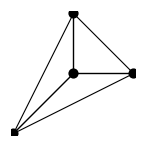

```mathematica
Graphics[{EdgeForm[Black],FaceForm[],Polygon@Take[fanGen,-Length[fanGen]+1], Line/@Thread[{Take[fanGen,-4], First[fanGen]}, List, 1], PointSize[.05],Point@fanGen}]
```

```mathematica
fanV = ArrayPad[fanGen, {{0,0}, {0,1}}, 1]
```

{{0,0,1},{1,0,1},{0,1,1},{-1,-1,1}}

```mathematica
Solve[Thread[fanVᵀ.Array[a,Length[fanGen]]==0], Array[a,Length[fanGen]], Integers]
fanQ = Array[a,Length[fanGen]]/.First[%]/.{{C[1]->-1}}
fanVQ = Join[fanVᵀ, %]ᵀ;
fanVQ//MatrixForm
```

{{a[1]→ConditionalExpression[3 C[1], C[1]∈ℤ],a[2]→ConditionalExpression[-C[1], C[1]∈ℤ],a[3]→ConditionalExpression[-C[1], C[1]∈ℤ],a[4]→ConditionalExpression[-C[1], C[1]∈ℤ]}}

{{-3,1,1,1}}

(0 | 0 | 1 | -3
1 | 0 | 1 | 1
0 | 1 | 1 | 1
-1 | -1 | 1 | 1)

```mathematica
CSMDef = Thread[Array[z,Length[fanQ]]->Table[Product[a[i]^fanQ[[A, i]], {i,Length[fanGen]}], {A, 1, Length[fanQ]}]]
```

{z[1]→(a[2] a[3] a[4])/a[1]^3}

```mathematica
H[X_,Y_]=Sum[a[i]X^fanVQ[[i,1]]Y^fanVQ[[i,2]], {i,Length[fanVQ]}]
```

a[1]+X a[2]+Y a[3]+a[4]/(X Y)

```mathematica
H[X,Y]/a[1]/.{X->xc X, Y->yc Y}//Expand
H1[X_,Y_]=%/.{xc->a[1]/a[2], yc->a[1]/a[3]}/.{(a[2] a[3] a[4])/a[1]^3->z}
```

1+(X xc a[2])/a[1]+(Y yc a[3])/a[1]+a[4]/(X xc Y yc a[1])

1+X+Y+z/(X Y)

## LV Scattering Diagram

```mathematica
(* Boris *)
ClearAll[repCh];
repCh={Ch[mF_,mB_][1]:>-{1,mF,mB,-(mB^2/2)+mB mF},Ch[mF_,mB_]:>{1,mF,mB,-(mB^2/2)+mB mF},GV[mF_,mB_,n_]:>{0,mF,mB,n}};
```

```mathematica
(* Boris *)
ClearAll[MonodromyOnCharge];
MonodromyOnCharge[M_,gam_]:=Module[{},
If[Length[M]==0,gam,
If[ArrayDepth[M]==2,
(*a single matrix*)
gam.Sigma.Inverse[M].Inverse[Sigma],
(*a list of matrices*)
MonodromyOnCharge[Drop[M,1],gam.Sigma.Inverse[First[M]].Inverse[Sigma]]
]
]
];
```

```mathematica
ZLV[{r,dF,dB,ch2},T,m]
Coefficient[%,{r,dF,dB,ch2}]
```

-ch2+dF m+(m^2 r)/2+2 dF T-m r T-4 r T^2+dB (-m+T)

{m^2/2-m T-4 T^2,m+2 T,-m+T,-1}

```mathematica
A = Simplify@ComplexExpand[1/4/r Re[Exp[-I psi]ZLV[{r,dF,dB,ch2},s+I t,m1+I m2]]]
```

1/(8 r)((-2 ch2-2 dB m1+2 dF m1+m1^2 r-m2^2 r+2 dB s+4 dF s-2 m1 r s-8 r s^2+2 m2 r t+8 r t^2) Cos[psi]+2 (m1 r (m2-t)+dB (-m2+t)+dF (m2+2 t)-r s (m2+8 t)) Sin[psi])

```mathematica
Simplify@Series[A/.{s->l s,t->l t}, {l,0,10}]
```

((-2 ch2-2 dB m1+2 dF m1+m1^2 r-m2^2 r) Cos[psi]+2 m2 (-dB+dF+m1 r) Sin[psi])/(8 r)+(((dB s+2 dF s-m1 r s+m2 r t) Cos[psi]+(-m2 r s+(dB+2 dF-m1 r) t) Sin[psi]) l)/(4 r)+((-s^2+t^2) Cos[psi]-2 s t Sin[psi]) l^2+O[l]^11

```mathematica
Q = 1/2D[A,{{s,t},2}]
b = 1/2D[A,{{s,t}}]/.{s->0,t->0}
```

{{-Cos[psi],-Sin[psi]},{-Sin[psi],Cos[psi]}}

{((2 dB+4 dF-2 m1 r) Cos[psi]-2 m2 r Sin[psi])/(16 r),(2 m2 r Cos[psi]+2 (dB+2 dF-m1 r) Sin[psi])/(16 r)}

```mathematica
M = 1/2Simplify@D[Expand[U^2 A/.{s->S/U,t->T/U}],{{S,T,U},2}]
```

{{-Cos[psi],-Sin[psi],((dB+2 dF-m1 r) Cos[psi]-m2 r Sin[psi])/(8 r)},{-Sin[psi],Cos[psi],(m2 r Cos[psi]+(dB+2 dF-m1 r) Sin[psi])/(8 r)},{((dB+2 dF-m1 r) Cos[psi]-m2 r Sin[psi])/(8 r),(m2 r Cos[psi]+(dB+2 dF-m1 r) Sin[psi])/(8 r),((-2 ch2-2 dB m1+2 dF m1+m1^2 r-m2^2 r) Cos[psi]+2 m2 (-dB+dF+m1 r) Sin[psi])/(8 r)}}

```mathematica
FullSimplify[Det[M]]//Expand
FullSimplify[%-Expand[-Cos[psi]/4 BogomolovDiscriminant[{r,dF,dB,ch2}]]/.{m2->0}]
```

-9/64 m1^2 Cos[psi]+9/64 m2^2 Cos[psi]-(dB^2 Cos[psi])/(64 r^2)-(dB dF Cos[psi])/(16 r^2)-(dF^2 Cos[psi])/(16 r^2)+(ch2 Cos[psi])/(4 r)+(9 dB m1 Cos[psi])/(32 r)-(3 dF m1 Cos[psi])/(16 r)-9/32 m1 m2 Sin[psi]+(9 dB m2 Sin[psi])/(32 r)-(3 dF m2 Sin[psi])/(16 r)

-((-3 dB+2 dF+3 m1 r)^2 Cos[psi])/(64 r^2)

```mathematica
Eigenvalues[Q]
```

{-1,1}

```mathematica
{s0,t0}=Simplify[Inverse[Q].(-b)]
```

{(dB+2 dF-m1 r)/(8 r),-m2/8}

```mathematica
Fp = Simplify[A/.{s->s0+s1,t->t0+t1}]
```

1/(64 r^2)((dB^2+4 dF^2+12 dF m1 r+2 dB (2 dF-9 m1 r)+r (-16 ch2+r (9 m1^2-9 m2^2-64 s1^2+64 t1^2))) Cos[psi]+2 r (-9 dB m2+6 dF m2+9 m1 m2 r-64 r s1 t1) Sin[psi])

```mathematica
(Fp/.{s1->0,t1->0})-Simplify[(A/.{s->0,t->0})-bᵀ.Inverse[Q].b]//Simplify
```

0

```mathematica
ClearAll[Rays];
Rays[{r_,dF_,dB_,ch2_},t_,psi_,m_:0]:=(ch2+(dB-dF) Re[m]-(dB+2 dF) t Tan[psi]+(dB-dF) Im[m] Tan[psi])/(dB+2 dF)/;r==0;
Rays[{r_,dF_,dB_,ch2_},t_,psi_,m_:0]:=-1/(8 r)(-dB-2 dF+r Re[m]+r (8 t+Im[m]) Tan[psi]+Sec[psi] √(Cos[psi]^2 ((dB+2 dF)^2+9 r^2 (-Im[m]+Re[m]) (Im[m]+Re[m])-2 r (8 ch2+(9 dB-6 dF) Re[m])+r^2 (8 t+Im[m])^2 Sec[psi]^2+6 r Im[m] (-3 dB+2 dF+3 r Re[m]) Tan[psi])));
```

```mathematica
Wall[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},{s_,t_},m_:0]:=(cch2 (dB+2 dF-m r)-ch2 (ddB+2 ddF-m rr)+1/2 m (-6 dB ddF+6 ddB dF-ddB m r+4 ddF m r+(dB-4 dF) m rr)+8 (-((cch2+(ddB-ddF) m) r)+(ch2+(dB-dF) m) rr) s+4 (ddB r+2 ddF r-(dB+2 dF) rr) (s^2+t^2))/(4 (ddB r+2 ddF r-dB rr-2 dF rr));
```

```mathematica
WallRadius[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},m_:0]:=(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2);
```

```mathematica
WallCircle[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},m_:0]:=Module[{R},
R=WallRadius[{r,dF,dB,ch2},{rr,ddF,ddB,cch2},m];
If[R>0,Circle[{(cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr)/(ddB r+2 ddF r-dB rr-2 dF rr),0},Sqrt[R],{0,Pi}],{}]];
```

164

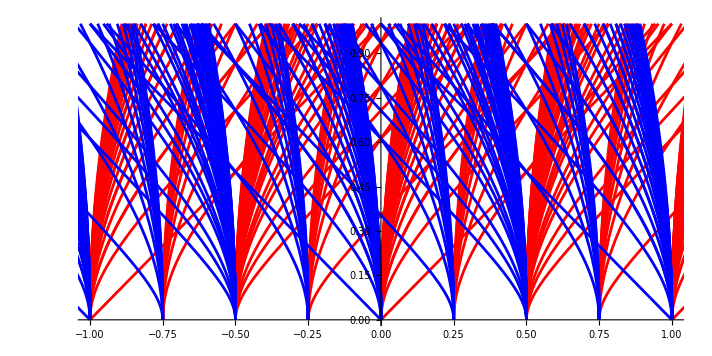

```mathematica
plt = With[{m=1/10,psi=0},Module[{charges1, rays},
rays = Table[
Tooltip[
Style[
{Rays[c/.repCh,t,psi,m], t},
If[First[c/.repCh]>0, Blue, Red]
], c],
 {c, charges}];
ParametricPlot[rays, {t,0,1},
PlotRange->{{-1,1},{0,1}}
]]]
```

```mathematica
{m/4,(m+1)/4,(1-m)/2,(m+2)/4,(m+3)/4,1-m/2}
```

```mathematica
<|1/40->{Ch[1,2],-Ch[0,0]},11/40->{Ch[1,1],-Ch[0,-1]},9/20->{Ch[2,1],-Ch[1,1]},21/40->{Ch[2,2],-Ch[1,0]},31/40->{Ch[3,3],-Ch[2,1]},19/20->{Ch[3,2],-Ch[2,2]}|>
```

```mathematica
With[{m=1/10, psi=0},
charges = Flatten@Table[s Ch[p,q],{p,-3,3},{q,-3,3},{s,{-1,1}}];
charges = Select[charges,-1<=Rays[#/.repCh,0,0,m]<=1&];
A =KeySort[GroupBy[charges,Rays[#/.repCh,0,0,m]&]];
casc = Function[s, SortBy[N@Rays[#/.repCh,1,0,m]&][s][[{1,-1}]]]/@A;

rays = Table[
Tooltip[
Style[
{Rays[c/.repCh,t,psi,m], t},
If[First[c/.repCh]>0, Blue, Red]
], c],
 {c, charges}];
rays1 = Table[
Tooltip[
Style[
{Rays[c/.repCh,t,psi,m], t},
Directive[Thickness[.004], Brown]
], c],
 {c, helixCharges}];
plt = ParametricPlot[rays, {t,0,1},
PlotRange->{{-1,1},{0,1}}];
plt1=ParametricPlot[rays1, {t,0,1},
PlotRange->{{-1,1},{0,1}}];
]
```

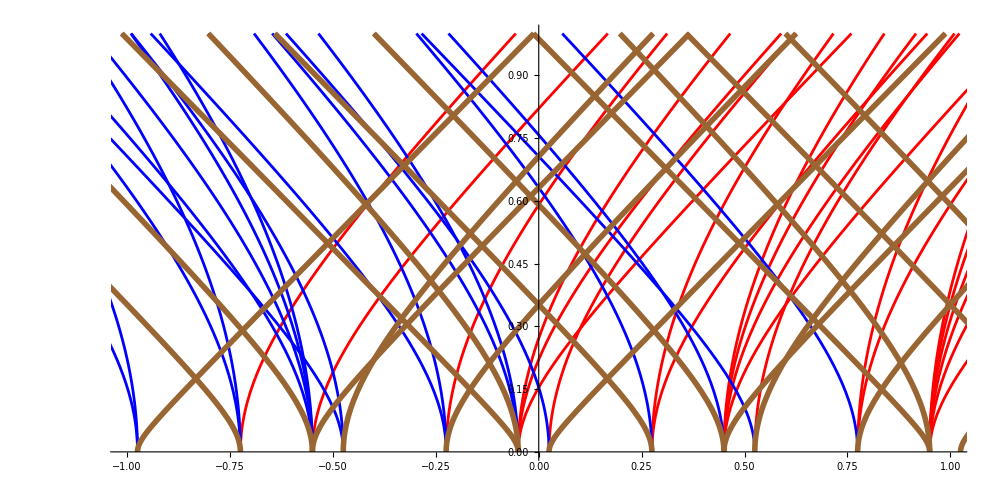

```mathematica
Show[plt,plt1]
```

```mathematica
DSZ@@{Ch[0,0],-Ch[-1,0]}/.repCh
```

2

```mathematica
{2,1}.{Ch[0,0],-Ch[-1,0]}/.repCh
```

{1,1,0,0}

```mathematica
DSZ@@#&/@Values[casc]/.repCh
```

{4,4,2,4,4,2}

```mathematica
(* spectral flow *)
ZLV[SpectralFlow[{r,dF,dB,ch2},{mF,mB}],T+mF/3,m+mB-(2 mF)/3]-ZLV[{r,dF,dB,ch2},T,m]//Simplify
```

0

```mathematica
Assuming[m∈Reals, Expand@Simplify@Rays[SpectralFlow[Ch[p,q]/.repCh,{3k,2k}],0,0,m]]
```

k-m/8+p/4-1/8 √((3 m+2 p-3 q)^2)+q/8

```mathematica
Expand@Assuming[(3 m-3 mB+2 mF)>0, Simplify[Rays[Ch[mF,mB]/.repCh, 0,0,m]/.{Re[m]->m,Im[m]->0}]]
```

-m/2+mB/2

```mathematica
Expand@Assuming[(3 m-3 mB+2 mF)<0, Simplify[Rays[Ch[mF,mB]/.repCh, 0,0,m]/.{Re[m]->m,Im[m]->0}]]
```

m/4-mB/4+mF/2

```mathematica
Expand[1/8D[ZLV[{-1,0,0,0},T,m], T]]
```

m/8+T

## Initial positions

```mathematica
FullSimplify[Rays[{r,dF,dB,ch2},0,0,m]/.{Re[m]->m,Im[m]->0}]
```

(dB+2 dF-m r-√(dB^2-16 ch2 r+2 dB (2 dF-9 m r)+(2 dF+3 m r)^2))/(8 r)

```mathematica
Flatten@Table[Rays[s Ch[p,q]/.repCh,0,0,1/10], {p,-20,20},{q,-20,20},{s,{-1,1}}];
Sort@DeleteDuplicates@Mod[%,1]
```

{1/40,11/40,9/20,21/40,31/40,19/20}

```mathematica
With[{m=Mod[-1-17812/98598,1]},
{m/4,(m+1)/4,(1-m)/2,(m+2)/4,(m+3)/4,1-m/2}
]
```

{40393/197196,22423/49299,4453/49299,138991/197196,94145/98598,58205/98598}

```mathematica
Reduce[0<=m/4<(m+1)/4<(1-m)/2<(m+2)/4<(m+3)/4<1-m/2<=1,m]
```

0<m<1/3

```mathematica
Reduce[{0<m/4<1,0<(m+1)/4<1,0<(1-m)/2<1,0<(m+2)/4<1,0<(m+3)/4<1,0<1-m/2<1},m]
```

0<m<1

```mathematica
0<=#<=1&/@{m/4,(m+1)/4,(1-m)/2,(m+2)/4,(m+3)/4,1-m/2}
Reduce[%,m]
```

{0≤m/4≤1,0≤(1+m)/4≤1,0≤(1-m)/2≤1,0≤(2+m)/4≤1,0≤(3+m)/4≤1,0≤1-m/2≤1}

0≤m≤1

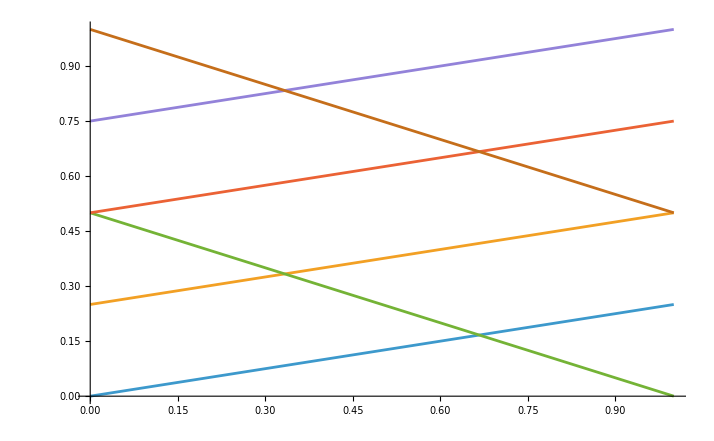

```mathematica
Plot[{m/4,(m+1)/4,(1-m)/2,(m+2)/4,(m+3)/4,1-m/2}, {m,0,1}]
```

```mathematica
charges = Flatten@Table[s Ch[p,q],{p,-10,10},{q,-10,10},{s,{-1,1}}];
A = GroupBy[charges,Mod[Rays[#/.repCh,0,0,1/10],1]&];
```

```mathematica
A = FullSimplify@ComplexExpand[Im[ZLV[{r,dF,dB,ch2},s+I t,m]**ZLV[{rr,ddF,ddB,cch2},s+I t,m]]]
```

1/2 t (-6 dB ddF m+6 ddB dF m-ddB m^2 r+4 ddF m^2 r+dB m^2 rr-4 dF m^2 rr-16 ddB m r s+16 ddF m r s+16 dB m rr s-16 dF m rr s+8 ddB r s^2+16 ddF r s^2-8 dB rr s^2-16 dF rr s^2+2 cch2 (dB+2 dF-r (m+8 s))-2 ch2 (ddB+2 ddF-rr (m+8 s))+8 ((ddB+2 ddF) r-(dB+2 dF) rr) t^2)

```mathematica
FullSimplify@Series[1/t A/.{s->s l,t->t l}, {l,0,11}]
A1=(Normal[%]/.{l->1})/4/DSZ[{r,dF,dB,ch2},{rr,ddF,ddB,cch2}]
```

(cch2 (dB+2 dF-m r)-ch2 (ddB+2 ddF-m rr)+1/2 m (-6 dB ddF+6 ddB dF-ddB m r+4 ddF m r+(dB-4 dF) m rr))+8 (-((cch2+(ddB-ddF) m) r)+(ch2+(dB-dF) m) rr) s l+4 (ddB r+2 ddF r-(dB+2 dF) rr) (s^2+t^2) l^2+O[l]^12

(cch2 (dB+2 dF-m r)-ch2 (ddB+2 ddF-m rr)+1/2 m (-6 dB ddF+6 ddB dF-ddB m r+4 ddF m r+(dB-4 dF) m rr)+8 (-((cch2+(ddB-ddF) m) r)+(ch2+(dB-dF) m) rr) s+4 (ddB r+2 ddF r-(dB+2 dF) rr) (s^2+t^2))/(4 (ddB r+2 ddF r-dB rr-2 dF rr))

```mathematica
Simplify[1/2D[A1,{{s,t},2}]]
```

{{1,0},{0,1}}

```mathematica
b=Together[1/2D[A1,{{s,t}}]/.{s->0,t->0}]
{s0,t0}=Simplify[Inverse[Q].(-b)]
```

{(-cch2 r-ddB m r+ddF m r+ch2 rr+dB m rr-dF m rr)/(ddB r+2 ddF r-dB rr-2 dF rr),0}

{(cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr)/(ddB r+2 ddF r-dB rr-2 dF rr),0}

```mathematica
FullSimplify[(s-s0)^2+(t-t0)^2/.First@Solve[A1==0,t]]
```

(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2)

```mathematica
A1
```

(cch2 (dB+2 dF-m r)-ch2 (ddB+2 ddF-m rr)+1/2 m (-6 dB ddF+6 ddB dF-ddB m r+4 ddF m r+(dB-4 dF) m rr)+8 (-((cch2+(ddB-ddF) m) r)+(ch2+(dB-dF) m) rr) s+4 (ddB r+2 ddF r-(dB+2 dF) rr) (s^2+t^2))/(4 (ddB r+2 ddF r-dB rr-2 dF rr))

1/8 (-m+3 √(m^2))

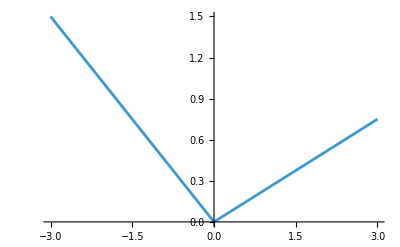

```mathematica
Rays[Ch[0,0]/.repCh,0,0,m]/.{Im[m]->0,Re[m]->m}//Simplify
Plot[%, {m,-3,3}]
```

```mathematica
ZLV[Ch[p,q]/.repCh,T,m]
Solve[%==0,T]
```

m^2/2+m p-p q+q^2/2-m T+2 p T-4 T^2+q (-m+T)

{{T→1/4 (m+2 p-q)},{T→1/2 (-m+q)}}

```mathematica
ToFB[{1,1,-1,0}]
```

{1,1,0,0}

```mathematica
ToFB[{1,2,-1,3/2}]
```

{1,2,1,3/2}

## initial rays as a function of m

```mathematica
With[{m=2/3+1/10},Module[{charges,casc},
charges = Flatten@Table[s Ch[p,q],{p,-20,20},{q,-20,20},{s,{-1,1}}];
charges = Select[charges,0<=Rays[#/.repCh,0,0,m]<=1&];
casc = KeySort[GroupBy[charges,Rays[#/.repCh,0,0,m]&]];
Function[s, SortBy[N@Rays[#/.repCh,1,0,m]&][s][[{1,-1}]]]/@casc
]]
```

<|7/60→{Ch[1,1],-Ch[0,1]},23/120→{Ch[1,2],-Ch[0,0]},53/120→{Ch[2,3],-Ch[1,1]},37/60→{Ch[2,2],-Ch[1,2]},83/120→{Ch[3,4],-Ch[2,2]},113/120→{Ch[3,3],-Ch[2,1]}|>

## LV: checking for other symmetries of the LV diagram

```mathematica
Manipulate[Show[plt/.{l_Line:>{Opacity[.1],l}}, plt/.{l_Line:>Translate[l,{L,0}]}], {{L,1},-2.5,2.5,.001}]
```

## XY scattering diagram

```mathematica
ZLV[{-1,0,0,0},T,m]
```

-m^2/2+m T+4 T^2

```mathematica
XYRay[{r_,dF_,dB_,ch2_},{x_,y_},mu_]:=r y+(2dF+dB)x+(dF-dB)mu-ch2;
```

```mathematica
{Re[Exp[-I psi]T]/Cos[psi], -Re[Exp[-I psi]TD]/Cos[psi]}/.{TD->ZLV[{-1,0,0,0},T,m]}/.{T->s+I t,psi->0}//ComplexExpand//FullSimplify//Expand
```

{s,m^2/2-m s-4 s^2+4 t^2}

```mathematica
Solve[Thread[{s,m^2/2-m s-4 s^2+4 t^2}=={x,y}],{s,t}]//Simplify
```

{{s→x,t→-1/2 √(-m^2/2+m x+4 x^2+y)},{s→x,t→1/2 √(-m^2/2+m x+4 x^2+y)}}

```mathematica
Solve[-m^2/2+m x+4 x^2+y==0,y]//Expand
```

{{y→m^2/2-m x-4 x^2}}

```mathematica
charges = Flatten@Table[s Ch[p,q],{p,-3,3},{q,-3,3},{s,{-1,1}}];
A = GroupBy[charges,Mod[Rays[#/.repCh,0,0,0],1]&];
```

```mathematica
XYRay[#/.repCh,{x,y},mu]&/@charges;
XYrays = Flatten@(y/.Solve[#==0,y]&/@%);
```

```mathematica
XYrays=Tooltip[y/.First@Solve[XYRay[#/.repCh,{x,y},mu]==0, y], #]&/@charges;
```

```mathematica
XYrays[[10]]
```

1/2 (-7+8 mu+10 x)

```mathematica
helixCharges = {Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]};
helixCharges = Flatten@Table[s c/.{Ch[p_,q_]:>Ch[p+3k,q+2k]}, {k,-1,1},{c,helixCharges}, {s,{-1,1}}]
```

{-Ch[-3,-2],Ch[-3,-2],-Ch[-2,-2],Ch[-2,-2],-Ch[-2,-1],Ch[-2,-1],-Ch[-1,-1],Ch[-1,-1],-Ch[0,0],Ch[0,0],-Ch[1,0],Ch[1,0],-Ch[1,1],Ch[1,1],-Ch[2,1],Ch[2,1],-Ch[3,2],Ch[3,2],-Ch[4,2],Ch[4,2],-Ch[4,3],Ch[4,3],-Ch[5,3],Ch[5,3]}

```mathematica
helixRays=Tooltip[y/.First@Solve[XYRay[#/.repCh,{x,y},mu]==0, y], #]&/@helixCharges;
```

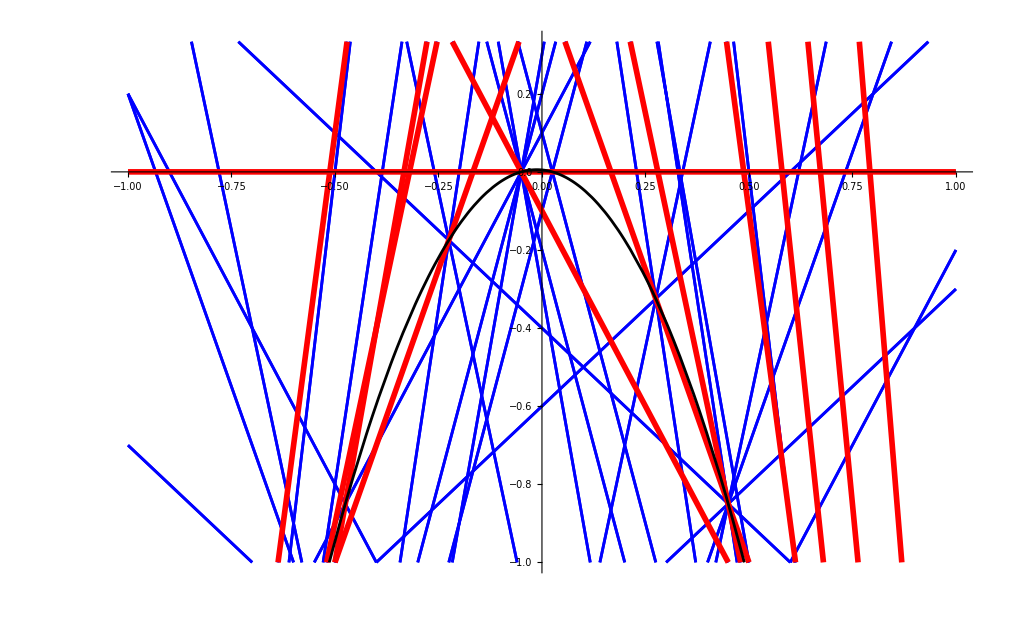

```mathematica
With[{m=1/10},Block[{mu=1/10},
Show[{
Plot[XYrays, {x,-1,1},
PlotRange->{{-1,1},{-1,1/3}},
PlotStyle->Directive[Thickness[.002], Blue]
],
Plot[helixRays, {x,-1,1},
PlotRange->{{-1,1},{-1,1/3}},
PlotStyle->Directive[Thickness[.004], Red]
],
Plot[m^2/2-m x-4 x^2,{x,-3,3},
PlotRange->{{-1,1},{-1,1}},
PlotStyle->Directive[Black]
]
}]
]]
```

## Checking Massless objects at conifold points

```mathematica
A = Numerator@Together[MirrorCurveJ[m,u]-j]
```

1-24 m u^2-72 u^3+240 m^2 u^4+1152 m u^5+1728 u^6-1280 m^3 u^6-6912 m^2 u^7-13824 m u^8-j m u^8+3840 m^4 u^8-13824 u^9-j u^9+18432 m^3 u^9+27648 m^2 u^10+8 j m^2 u^10-6144 m^5 u^10+36 j m u^11-18432 m^4 u^11+27 j u^12-16 j m^3 u^12+4096 m^6 u^12

```mathematica
Simplify@Discriminant[A,u]
```

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12)

```mathematica
A1 = A/.First@Solve[(-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12)==0,j]//FullSimplify
%/.{u->-8m/9}//Simplify
```

-1/(16777216 m^9)(8 m+9 u)^2 (-939524096 m^11 u^8+1073741824 m^12 u^10-1417176 m^2 u^5 (-2+27 u^3)-4782969 u^7 (-1+27 u^3)-33554432 m^10 u^6 (-10+79 u^3)+531441 m u^6 (-7+108 u^3)-6291456 m^9 u^4 (10-168 u^3+267 u^6)+3145728 m^8 u^2 (2-51 u^3+324 u^6)-248832 m^5 u^2 (4-144 u^3+1215 u^6)+186624 m^4 u^3 (8-306 u^3+3159 u^6)-104976 m^3 u^4 (20-792 u^3+14823 u^6)+65536 m^7 (-4+9 u^3 (8-21 u^3+324 u^6))-147456 m^6 u (-4+9 u^3 (14-174 u^3+2511 u^6)))

0

```mathematica
A2=Numerator[A1]/-(8 m+9 u)^2
```

-939524096 m^11 u^8+1073741824 m^12 u^10-1417176 m^2 u^5 (-2+27 u^3)-4782969 u^7 (-1+27 u^3)-33554432 m^10 u^6 (-10+79 u^3)+531441 m u^6 (-7+108 u^3)-6291456 m^9 u^4 (10-168 u^3+267 u^6)+3145728 m^8 u^2 (2-51 u^3+324 u^6)-248832 m^5 u^2 (4-144 u^3+1215 u^6)+186624 m^4 u^3 (8-306 u^3+3159 u^6)-104976 m^3 u^4 (20-792 u^3+14823 u^6)+65536 m^7 (-4+9 u^3 (8-21 u^3+324 u^6))-147456 m^6 u (-4+9 u^3 (14-174 u^3+2511 u^6))

```mathematica
bpoints = ReIm[u]/.NSolve[A2==0/.{m->N[.1,300]}, u, WorkingPrecision->300];
```

NSolve::precw: The precision of the argument function ({-0.00939524 u^8+«16»+0.0065536 (-4+9 u^3 (8-21 Power[«2»]+324 Power[«2»]))-0.147456 u (-4+9 u^3 (14-174 Power[«2»]+2511 Power[«2»]))}) is less than WorkingPrecision (300).

```mathematica
Length[bpoints]
```

10

```mathematica
Simplify@Discriminant[A2,u]
```

-81129638414606681695789005144064 m^42 (27+256 m^3)^6 (243+256 m^3)^18 (-19683-124416 m^3+65536 m^6)^9

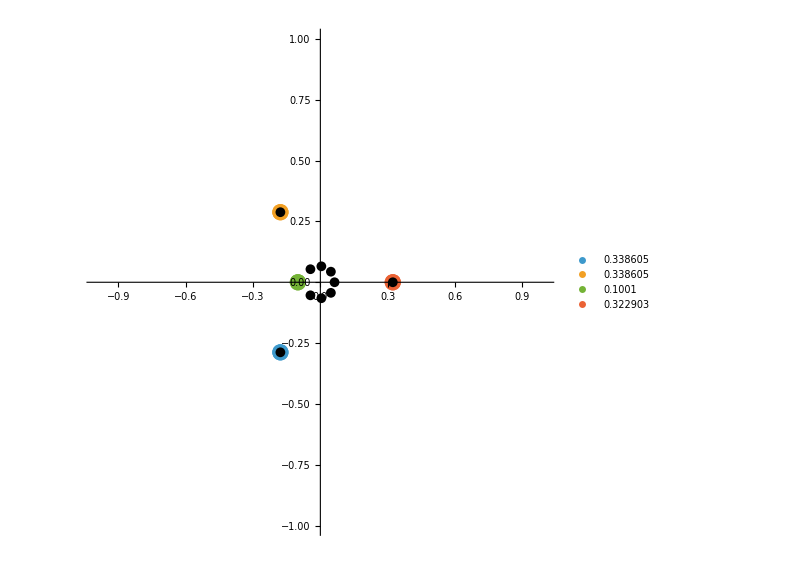

```mathematica
Show[PlotURoots[N[.1,300]], Graphics[{PointSize[.012], Point[bpoints]}]]
```

```mathematica
1728KleinInvariantJ[I]
```

1728

```mathematica
1728KleinInvariantJ[Exp[2Pi I/3]]
```

0

```mathematica
D[KleinInvariantJ[tau],{tau,2}]/.{tau->I}//N
```

-28.7356

```mathematica
D[KleinInvariantJ[tau],{tau,3}]/.{tau->Exp[2Pi I/3]}//N
```

-2.19688×10^-14-158.837 ⅈ

WolframAlphaQueryResults

## Wall radius in terms of DSZ and Wall center

```mathematica
cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr/.{
dF->Subscript[d,F],
dB->Subscript[d,F],
ddB->Subscript[d,F],
}
```

ReplaceAll::reps: {dF→d_F,dB→d_F,ddB→d'_F,Null} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr/.{dF→d_F,dB→d_F,ddB→d'_F,Null}

```mathematica
DSZ[{r,dF,dB,ch2},{rr,ddF,ddB,cch2}]
```

ddB r+2 ddF r-dB rr-2 dF rr

```mathematica
FullSimplify[Sqrt[(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2)]]
```

1/(2 √2)(√((r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(ddB r+2 ddF r-(dB+2 dF) rr)^2))

```mathematica
tmp = ExpandAll[(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2)];
```

```mathematica
FullSimplify[Sqrt[tmp], {(r|dF|dB|ch2|rr|ddF|ddB|cch2)∈Integers,0<m<1}]
```

1/(2 √2)(√((r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(ddB r+2 ddF r-(dB+2 dF) rr)^2))

```mathematica
tmp = ExpandAll[(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)]
FullSimplify[Sqrt[%], {(r|dF|dB|ch2|rr|ddF|ddB|cch2)∈Integers,0<m<1}]
```

-2 cch2 dB ddB r+2 ch2 ddB^2 r-4 cch2 dB ddF r+8 ch2 ddB ddF r+8 ch2 ddF^2 r-4 cch2 ddB dF r-8 cch2 ddF dF r+6 dB ddB ddF m r+12 dB ddF^2 m r-6 ddB^2 dF m r-12 ddB ddF dF m r+8 cch2^2 r^2+18 cch2 ddB m r^2-12 cch2 ddF m r^2+9 ddB^2 m^2 r^2-18 ddB ddF m^2 r^2+2 cch2 dB^2 rr-2 ch2 dB ddB rr-4 ch2 dB ddF rr+8 cch2 dB dF rr-4 ch2 ddB dF rr-8 ch2 ddF dF rr+8 cch2 dF^2 rr-6 dB^2 ddF m rr+6 dB ddB dF m rr-12 dB ddF dF m rr+12 ddB dF^2 m rr-16 cch2 ch2 r rr-18 cch2 dB m r rr-18 ch2 ddB m r rr+12 ch2 ddF m r rr+12 cch2 dF m r rr-18 dB ddB m^2 r rr+18 dB ddF m^2 r rr+18 ddB dF m^2 r rr+8 ch2^2 rr^2+18 ch2 dB m rr^2-12 ch2 dF m rr^2+9 dB^2 m^2 rr^2-18 dB dF m^2 rr^2

√(8 cch2^2 r^2+r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF+3 dB ddF m-3 ddB dF m)+9 ddB (ddB-2 ddF) m^2 r)-2 ((dB+2 dF) (ch2 ddB+2 ch2 ddF+3 dB ddF m-3 ddB dF m)+3 m (3 ch2 ddB-2 ch2 ddF+3 dB ddB m-3 dB ddF m-3 ddB dF m) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2+2 cch2 (r (-((ddB+2 ddF) (dB+2 dF))+3 (3 ddB-2 ddF) m r)+((dB+2 dF)^2+(-8 ch2-9 dB m+6 dF m) r) rr))

```mathematica
sol=Solve[{ddB r+2 ddF r-dB rr-2 dF rr==d, cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr==c},{dB,ch2}]
```

{{dB→-(d-ddB r-2 ddF r+2 dF rr)/rr,ch2→-(c-d m-cch2 r+3 ddF m r-3 dF m rr)/rr}}

```mathematica
FullSimplify[tmp/.First[sol]]//ExpandAll
```

8 c^2+2 c d m-d^2 m^2+(2 cch2 d^2)/rr-(2 c d ddB)/rr-(4 c d ddF)/rr+(2 d^2 ddB m)/rr-(2 d^2 ddF m)/rr

```mathematica
FullSimplify[(2 cch2 d^2)/rr-(2 c d ddB)/rr-(4 c d ddF)/rr+(2 d^2 ddB m)/rr-(2 d^2 ddF m)/rr]
```

(2 d (cch2 d-c (ddB+2 ddF)+d (ddB-ddF) m))/rr

## Monodromies

```mathematica
M1 = {{1,0,0,0},{0,1,0,0},{0,0,1,1},{0,0,0,1}};
M2={{1,0,0,0},{0,1,0,0},{0,-1,-1,1},{0,-2,-4,3}};
M3={{1,0,0,0},{0,1,0,0},{1/2,0,-2,1},{3/2,0,-9,4}};
M4={{1,0,0,0},{0,1,0,0},{1/2,0,4,1},{-3/2,0,-9,-2}};
```

```mathematica
MatrixForm/@{M1,M2,M3,M4}
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | -1 | -1 | 1
0 | -2 | -4 | 3),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1/2 | 0 | -2 | 1
3/2 | 0 | -9 | 4),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1/2 | 0 | 4 | 1
-3/2 | 0 | -9 | -2)}

```mathematica
M3.M2.M1.M4//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | 0 | 1 | 0
4 | 1 | 8 | 1)

```mathematica
A = FullSimplify[{r,dF,dB,ch2}-DSZ[{rr,ddF,ddB,cch2},{r,dF,dB,ch2}]{rr,ddF,ddB,cch2}]
```

{r+(ddB+2 ddF) r rr-(dB+2 dF) rr^2,dF+ddB ddF r+2 ddF^2 r-ddF (dB+2 dF) rr,dB+ddB (ddB+2 ddF) r-ddB (dB+2 dF) rr,ch2+cch2 (ddB+2 ddF) r-cch2 (dB+2 dF) rr}

```mathematica
STwist[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_}]:={r+(ddB+2 ddF) r rr-(dB+2 dF) rr^2,dF+ddB ddF r+2 ddF^2 r-ddF (dB+2 dF) rr,dB+ddB (ddB+2 ddF) r-ddB (dB+2 dF) rr,ch2+cch2 (ddB+2 ddF) r-cch2 (dB+2 dF) rr};
```

```mathematica
STwist[{r,dF,dB,ch2},Ch[mF,mB]/.repCh]//FullSimplify
```

{-dB-2 dF+(1+mB+2 mF) r,dF-dB mF-2 dF mF+mF (mB+2 mF) r,dB-(dB+2 dF) mB+mB (mB+2 mF) r,ch2-1/2 mB (mB-2 mF) (-dB-2 dF+mB r+2 mF r)}

```mathematica
{r,dF,dB,ch2}.Sigma.{1,m,T,TD}ᵀ
```

-ch2+(-dB+dF) m+(dB+2 dF) T-r TD

```mathematica
tmp=IdentityMatrix[4]-Simplify@Outer[Times,D[DSZ[{rr,ddF,ddB,cch2},{r,dF,dB,ch2}],{{r,dF,dB,ch2}}],{rr,ddF,ddB,cch2}]
```

{{1+(ddB+2 ddF) rr,ddF (ddB+2 ddF),ddB (ddB+2 ddF),cch2 (ddB+2 ddF)},{-2 rr^2,1-2 ddF rr,-2 ddB rr,-2 cch2 rr},{-rr^2,-ddF rr,1-ddB rr,-cch2 rr},{0,0,0,1}}

```mathematica
g = Simplify[tmp/.{rr->1,ddF->mF,ddB->mB,cch2->-mB^2/2+mB mF}]
```

{{1+mB+2 mF,mF (mB+2 mF),mB (mB+2 mF),-mB^3/2+2 mB mF^2},{-2,1-2 mF,-2 mB,mB (mB-2 mF)},{-1,-mF,1-mB,1/2 mB (mB-2 mF)},{0,0,0,1}}

```mathematica
MST[mF_,mB_]=Inverse[Sigma].Inverse[g].Sigma//Simplify
```

{{1,0,0,0},{0,1,0,0},{1/2 mB (mB-2 mF),-mB+mF,1+mB+2 mF,-1},{1/2 mB (mB^2-4 mF^2),-mB^2-mB mF+2 mF^2,(mB+2 mF)^2,1-mB-2 mF}}

```mathematica
Inverse[MST[0,0]]==M1
```

True

```mathematica
Inverse[MST[1,0]]==M2
```

True

```mathematica
Inverse[MST[1,1]]==M3
```

True

```mathematica
Inverse[MST[-1,-1]]==M4
```

True

```mathematica
MST[mF,mB].{1,m,T,TD}
1/8D[%[[4]]/.{T->T[z],TD->TD[z]},z]/D[%[[3]]/.{T->T[z],TD->TD[z]},z]/.{TD'[z]->8tau T'[z]}//Simplify
Solve[%==tau, tau]
```

{1,m,1/2 mB (mB-2 mF)+m (-mB+mF)+(1+mB+2 mF) T-TD,1/2 mB (mB^2-4 mF^2)+m (-mB^2-mB mF+2 mF^2)+(mB+2 mF)^2 T+(1-mB-2 mF) TD}

(mB^2+4 mB (mF-2 tau)+4 (mF^2+2 tau-4 mF tau))/(8 (1+mB+2 mF-8 tau))

{{tau→1/8 (mB+2 mF)},{tau→1/8 (mB+2 mF)}}

```mathematica
A = SpectralFlow[{r,dF,dB,ch2},{3,2}];
tmp =D[A,{{r,dF,dB,ch2}}]ᵀ
A-{r,dF,dB,ch2}.tmp//Simplify
```

{{1,3,2,4},{0,1,0,2},{0,0,1,1},{0,0,0,1}}

{0,0,0,0}

```mathematica
Inverse[Sigma].Inverse[tmp].Sigma
```

{{1,0,0,0},{0,1,0,0},{1,0,1,0},{4,1,8,1}}

```mathematica
M1p={{1,0,0,0},{0,1,0,0},{-1/2,1,0,1},{-1/2,1,-1,1}};
M2p={{1,0,0,0},{0,1,0,0},{0,-1,3,1},{0,-2,-4,-1}};
M4p={{1,0,0,0},{0,1,0,0},{1/2,0,-2,1},{3/2,0,-9,4}};
```

```mathematica
MST[mF,mB]
```

{{1,0,0,0},{0,1,0,0},{1/2 mB (mB-2 mF),-mB+mF,1+mB+2 mF,-1},{1/2 mB (mB^2-4 mF^2),-mB^2-mB mF+2 mF^2,(mB+2 mF)^2,1-mB-2 mF}}

```mathematica
Reduce[Thread[Flatten[M4p-Inverse[MST[mF,mB]]]==0],{mF,mB}]
```

mF==1&&mB==1

```mathematica
Reduce[Thread[Flatten[M2p-Inverse[MST[mF,mB]]]==0],{mF,mB}]
```

False

{{1,0,0,0},{0,1,0,0},{1/2 (mB^2-2 mB mF) p,-((mB-mF) p),1+mB p+2 mF p,-p},{1/2 (mB^3-4 mB mF^2) p,-((mB^2+mB mF-2 mF^2) p),(mB+2 mF)^2 p,1-mB p-2 mF p}}

```mathematica
M2p-MatrixPower[MLVMST[mF,mB],p]
```

{{0,0,0,0},{0,0,0,0},{-1/2 (mB^2-2 mB mF) p,-1+(mB-mF) p,2-mB p-2 mF p,1+p},{-1/2 (mB^3-4 mB mF^2) p,-2+(mB^2+mB mF-2 mF^2) p,-4-(mB+2 mF)^2 p,-2+mB p+2 mF p}}

```mathematica
Solve[{-1-mB+mF==0,-2-mB-2 mF==0},{mF,mB}]
```

{{mF→-1/3,mB→-4/3}}

```mathematica
MatrixPower[M1p,p]
```

{{1,0,0,0},{0,1,0,0},{-1/2-(ⅈ (2^(-1-p) (1-ⅈ √3)^p+ⅈ 2^(-1-p) √3 (1-ⅈ √3)^p))/(2 √3)+(ⅈ (2^(-1-p) (1+ⅈ √3)^p-ⅈ 2^(-1-p) √3 (1+ⅈ √3)^p))/(2 √3),1+(ⅈ (2^(-1-p) (1-ⅈ √3)^p+ⅈ 2^(-1-p) √3 (1-ⅈ √3)^p))/(√3)-(ⅈ (2^(-1-p) (1+ⅈ √3)^p-ⅈ 2^(-1-p) √3 (1+ⅈ √3)^p))/(√3),-(ⅈ (2^(-1-p) (1-ⅈ √3)^p+ⅈ 2^(-1-p) √3 (1-ⅈ √3)^p))/(√3)+(ⅈ (2^(-1-p) (1+ⅈ √3)^p-ⅈ 2^(-1-p) √3 (1+ⅈ √3)^p))/(√3),1/2 (1+ⅈ/(√3)) (2^(-1-p) (1-ⅈ √3)^p+ⅈ 2^(-1-p) √3 (1-ⅈ √3)^p)+1/2 (1-ⅈ/(√3)) (2^(-1-p) (1+ⅈ √3)^p-ⅈ 2^(-1-p) √3 (1+ⅈ √3)^p)},{-(ⅈ 2^(-1-p) (1-ⅈ √3)^p)/(√3)+(ⅈ 2^(-1-p) (1+ⅈ √3)^p)/(√3),(ⅈ (1/2 (1-ⅈ √3))^p)/(√3)-(ⅈ (1/2 (1+ⅈ √3))^p)/(√3),-(ⅈ (1/2 (1-ⅈ √3))^p)/(√3)+(ⅈ (1/2 (1+ⅈ √3))^p)/(√3),2^(-1-p) (1+ⅈ/(√3)) (1-ⅈ √3)^p+2^(-1-p) (1-ⅈ/(√3)) (1+ⅈ √3)^p}}

```mathematica
MatrixPower[MLV.MST[0,0],p]
```

{{1,0,0,0},{0,1,0,0},{1/2+1/8 (-3-2 √2)^p (-2+√2)-1/8 (2+√2) (-3+2 √2)^p,-1/8+((-3-2 √2)^p (-2+√2))/(16 √2)+((2+√2) (-3+2 √2)^p)/(16 √2),((-3-2 √2)^p (-2+√2))/(2 √2)+((2+√2) (-3+2 √2)^p)/(2 √2),-((-3-2 √2)^p (-2+√2) (2+√2))/(8 √2)+((-2+√2) (2+√2) (-3+2 √2)^p)/(8 √2)},{1-1/2 (-3-2 √2)^p-1/2 (-3+2 √2)^p,-(-3-2 √2)^p/(4 √2)+(-3+2 √2)^p/(4 √2),-√2 (-3-2 √2)^p+√2 (-3+2 √2)^p,((-3-2 √2)^p (2+√2))/(2 √2)+((-2+√2) (-3+2 √2)^p)/(2 √2)}}

```mathematica
D[SpectralFlow[{r,dF,dB,ch2},{mF,mB}],{{r,dF,dB,ch2}}]ᵀ
Simplify[Inverse[Sigma].Inverse[%].Sigma]//Expand//MatrixForm
```

{{1,mF,mB,-mB^2/2+mB mF},{0,1,0,mB},{0,0,1,-mB+mF},{0,0,0,1}}

(1 | 0 | 0 | 0
mB-(2 mF)/3 | 1 | 0 | 0
mF/3 | 0 | 1 | 0
-mB^2/2+mB mF | -mB+mF | mB+2 mF | 1)

## Picard Fuchs redo

```mathematica
pf1[f_,z1_,z2_]:=z1 D[z1 D[f, z1]-z2 D[f, z2], z1]-z1 (2z1 D[f+2z1 D[f, z1]+z2 D[f, z2],z1]+z2 D[f+2z1 D[f, z1]+z2 D[f, z2],z2]);
pf2[f_,z1_,z2_]:=z2 D[z2 D[f, z2], z2]-z2(z2 D[2z1 D[f,z1]+z2 D[f,z2],z2]-z1 D[2z1 D[f,z1]+z2 D[f,z2],z1]);
```

```mathematica
trial = Series[-Log[u]-m u^2-2u^3-3/2m^2u^4-12m u^5-(15+10m^3/3)u^6, {u,0,6}]
```

-Log[u]-m u^2-2 u^3-(3 m^2 u^4)/2-12 m u^5-5/3 (9+2 m^3) u^6+O[u]^7

```mathematica
Solve[{z1==m u^2,z2==-u/m},{m,u}]//Simplify
```

{{m→z1^(1/3)/z2^(2/3),u→-z1^(1/3) z2^(1/3)},{m→-((-1)^(1/3) z1^(1/3))/z2^(2/3),u→(-1)^(1/3) z1^(1/3) z2^(1/3)},{m→((-1)^(2/3) z1^(1/3))/z2^(2/3),u→-(-1)^(2/3) z1^(1/3) z2^(1/3)}}

```mathematica
Expand[pf1[f[m,u]/.{m->((-1)^(2/3) z1^(1/3))/z2^(2/3),u->-(-1)^(2/3) z1^(1/3) z2^(1/3)},z1,z2]]/.{z1->m u^2,z2->-u/m}//PowerExpand
```

-2 m u^3 f^(0,1)[m,u]-m u^4 f^(0,2)[m,u]+1/3 m f^(1,0)[m,u]+1/3 m u f^(1,1)[m,u]+1/3 m^2 f^(2,0)[m,u]

```mathematica
Expand[pf2[f[m,u]/.{m->((-1)^(2/3) z1^(1/3))/z2^(2/3),u->-(-1)^(2/3) z1^(1/3) z2^(1/3)},z1,z2]]/.{z1->m u^2,z2->-u/m}//PowerExpand
```

1/9 u f^(0,1)[m,u]+1/9 u^2 f^(0,2)[m,u]+4/9 m f^(1,0)[m,u]-4/9 m u f^(1,1)[m,u]-u^2 f^(1,1)[m,u]+4/9 m^2 f^(2,0)[m,u]

```mathematica
-2 m u^3 Derivative[0,1][f][m,u]-m u^4 Derivative[0,2][f][m,u]+1/3 m Derivative[1,0][f][m,u]+1/3 m u Derivative[1,1][f][m,u]+1/3 m^2 Derivative[2,0][f][m,u]/.{Derivative[i_,j_][f][m,u]:>D1[f, {m,i},{u,j}]}
```

-2 m u^3 D1[f,{m,0},{u,1}]-m u^4 D1[f,{m,0},{u,2}]+1/3 m D1[f,{m,1},{u,0}]+1/3 m u D1[f,{m,1},{u,1}]+1/3 m^2 D1[f,{m,2},{u,0}]

```mathematica
1/9 u Derivative[0,1][f][m,u]+1/9 u^2 Derivative[0,2][f][m,u]+4/9 m Derivative[1,0][f][m,u]-4/9 m u Derivative[1,1][f][m,u]-u^2 Derivative[1,1][f][m,u]+4/9 m^2 Derivative[2,0][f][m,u]/.{Derivative[i_,j_][f][m,u]:>D1[f, {m,i},{u,j}]}
```

1/9 u D1[f,{m,0},{u,1}]+1/9 u^2 D1[f,{m,0},{u,2}]+4/9 m D1[f,{m,1},{u,0}]-4/9 m u D1[f,{m,1},{u,1}]-u^2 D1[f,{m,1},{u,1}]+4/9 m^2 D1[f,{m,2},{u,0}]

```mathematica
ClearAll[A1,A2];
A1[f_]:=-2 m u^3 D[f,{m,0},{u,1}]-m u^4 D[f,{m,0},{u,2}]+1/3 m D[f,{m,1},{u,0}]+1/3 m u D[f,{m,1},{u,1}]+1/3 m^2 D[f,{m,2},{u,0}];
A2[f_]:=1/9 u D[f,{m,0},{u,1}]+1/9 u^2 D[f,{m,0},{u,2}]+4/9 m D[f,{m,1},{u,0}]-4/9 m u D[f,{m,1},{u,1}]-u^2 D[f,{m,1},{u,1}]+4/9 m^2 D[f,{m,2},{u,0}];
```

```mathematica
Through[{A1,A2}[trial]]
```

{O[u]^7,O[u]^7}

```mathematica
Expand[FullSimplify[3A1[f[m,-1/u]]]]/.{u->-1/ut,m->λ}//Expand
```

-3 λ f^(0,2)[λ,ut]+λ f^(1,0)[λ,ut]-ut λ f^(1,1)[λ,ut]+λ^2 f^(2,0)[λ,ut]

```mathematica
Expand[FullSimplify[9A2[f[m,-1/u]]]]/.{u->-1/ut,m->λ}//Expand
```

ut f^(0,1)[λ,ut]+ut^2 f^(0,2)[λ,ut]+4 λ f^(1,0)[λ,ut]-9 f^(1,1)[λ,ut]+4 ut λ f^(1,1)[λ,ut]+4 λ^2 f^(2,0)[λ,ut]

```mathematica
Expand[3A1[f[m,u]]]
sol = First@Solve[%==0,Derivative[2,0][f][m,u]]
```

-6 m u^3 f^(0,1)[m,u]-3 m u^4 f^(0,2)[m,u]+m f^(1,0)[m,u]+m u f^(1,1)[m,u]+m^2 f^(2,0)[m,u]

{f^(2,0)[m,u]→(6 u^3 f^(0,1)[m,u]+3 u^4 f^(0,2)[m,u]-f^(1,0)[m,u]-u f^(1,1)[m,u])/m}

```mathematica
Expand[D[9/4A2[f[m,u]],u]]
```

1/4 f^(0,1)[m,u]+3/4 u f^(0,2)[m,u]+1/4 u^2 f^(0,3)[m,u]-9/2 u f^(1,1)[m,u]-m u f^(1,2)[m,u]-9/4 u^2 f^(1,2)[m,u]+m^2 f^(2,1)[m,u]

```mathematica
A3[f_]:=(8m ut-9)(-27+16m^3+36m ut-8m^2ut^2-ut^3+m ut^4)D[f,{ut,3}]+(-108m-128m^4+144m^2ut+27ut^2-64m^3ut^2-52m ut^3+24m^2ut^4)D[f,{ut,2}]+(-12m^2+9ut-18m ut^2+8m^2ut^3)D[f,ut];
```

```mathematica
Simplify[A3[f[m,-1/ut]]/.{ut->-1/u}]/.{f->Function[{m,u},Evaluate[trial]]}
```

O[u]^5

```mathematica
FullSimplify[A3[F[-1/ut]]/.{ut->-1/u}]
{B3,B2,B1}=Simplify[Coefficient[%,{Derivative[3][F][u],Derivative[2][F][u],Derivative[1][F][u]}]]
```

1/u(-((18 m u+9 u^2+4 m^2 (2+3 u^3)) F'[u])+(24 m^2+52 m u+(27-64 m^3) u^2-144 m^2 u^3-4 m (27+32 m^3) u^4) (2 F'[u]+u F''[u])-(8 m+9 u) (m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4) (6 F'[u]+u (6 F''[u]+u F^(3)[u])))

{u (-128 m^4 u^4-16 m^3 u^2 (-4+9 u^3)+9 u^2 (-1+27 u^3)+8 m^2 (-1+45 u^3)+m u (-17+540 u^3)),-896 m^4 u^4+27 u^2 (-1+54 u^3)+24 m^2 (-1+84 u^3)+m (-50 u+3132 u^4)+m^3 (320 u^2-864 u^5),-1024 m^4 u^3-32 m^3 u (-8+27 u^3)+9 u (-1+162 u^3)+16 m (-1+189 u^3)+(4 m^2 (-2+465 u^3))/u}

```mathematica
Series[B2/B3/.{m->1},{u,0,2}]
```

3/u-1/8-(1007 u)/64-(43225 u^2)/512+O[u]^3

```mathematica
Series[u B1/B3/.{m->1},{u,0,2}]
```

1/u-1/8-(1519 u)/64-(70617 u^2)/512+O[u]^3

```mathematica
matA = Simplify[{{0,1,0},{0,0,1},{0,-B1/B3,-B2/B3}}/.{m->1}]
```

{{0,1,0},{0,0,1},{0,(8+16 u-247 u^2-1860 u^3-2000 u^4-594 u^5)/(u^2 (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5)),(24+50 u-293 u^2-2016 u^3-2236 u^4-594 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5))}}

```mathematica
{{0,1,0},{0,0,1},{0,-b1,-b2}}.{y,u y',y''}
```

{u y',y'',-b1 u y'-b2 y''}

```mathematica
D[{F[u],F'[u],u F''[u]}, u]/.{Derivative[3][F][u]->-b2 Derivative[2][F][u]-b1 Derivative[1][F][u]-b0 F[u]}
D[Simplify[%/.{F[u]->u1,F'[u]->u2,F''[u]->u3/u}], {{u1,u2,u3}}]
```

{F'[u],F''[u],F''[u]+u (-b0 F[u]-b1 F'[u]-b2 F''[u])}

{{0,1,0},{0,0,1/u},{-b0 u,-b1 u,-b2+1/u}}

```mathematica
matA = Simplify[{{0,1,0},{0,0,1/u},{-b0 u,-b1 u,-b2+1/u}}/.{b0->0,b1->B1/B3,b2->B2/B3}/.{m->1}]
```

{{0,1,0},{0,0,1/u},{0,(8+16 u-247 u^2-1860 u^3-2000 u^4-594 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5)),(16+33 u-238 u^2-1656 u^3-1824 u^4-495 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5))}}

```mathematica
Am1=Limit[u matA,u->0]
```

{{0,0,0},{0,0,1},{0,-1,-2}}

```mathematica
MatrixExp[2Pi I Am1].{om1,2Pi I T,-(2Pi I)^2(TD-1/6)/4}
Expand[{%[[1]],%[[2]]/(2Pi I),-4%[[3]]/(2Pi I)^2+1/6}]
```

{om1,2 ⅈ (1+2 ⅈ π) π T+2 ⅈ π^3 (-1/6+TD),4 π^2 T+(1-2 ⅈ π) π^2 (-1/6+TD)}

{om1,-π^2/6+T+2 ⅈ π T+π^2 TD,(ⅈ π)/3+4 T+TD-2 ⅈ π TD}

```mathematica
MatrixForm/@JordanDecomposition[Am1]
```

{(0 | 0 | 1
-1 | -1 | 0
1 | 0 | 0),(-1 | 1 | 0
0 | -1 | 0
0 | 0 | 0)}

## Definitions to be added

```mathematica
Sigma:={{0,0,0,-1},{0,1,2,0},{0,-1,1,0},{-1,0,0,0}};
```

```mathematica
MLV={{1,0,0,0},{0,1,0,0},{1,0,1,0},{4,1,8,1}};
```

```mathematica
MSF[mF_,mB_]:={{1,mF,mB,-mB^2/2+mB mF},{0,1,0,mB},{0,0,1,-mB+mF},{0,0,0,1}};
```

```mathematica
MST[mF_,mB_] := {{1,0,0,0},{0,1,0,0},{1/2 mB (mB-2 mF),-mB+mF,1+mB+2 mF,-1},{1/2 mB (mB^2-4 mF^2),-mB^2-mB mF+2 mF^2,(mB+2 mF)^2,1-mB-2 mF}};
```

```mathematica
M1p={{1,0,0,0},{0,1,0,0},{-1/2,1,0,1},{-1/2,1,-1,1}};
M2p={{1,0,0,0},{0,1,0,0},{0,-1,3,1},{0,-2,-4,-1}};
```

```mathematica
MonodromyOnCharge[M_,gam_]:=gam.Sigma.Inverse[M].Inverse[Sigma];
```

```mathematica
MonodromyOnTau[M_,tau_]:=(M[[4,3]]+8 tau M[[4,4]])/(8 M[[3,3]]+64 tau M[[3,4]]);
```